## Metaengineering and Laws of Innovation

```mathematica
AnimationVideo[(ArrayPlot[ArrayPad[#,{6,6}],Mesh->True,MeshStyle->Opacity[.1],ImageSize->200]&/@CellularAutomaton["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Blinker"]["MatrixData"],0},24])[[i]], {i, 1, 24, 1}]
```

```mathematica
AnimationVideo[(ArrayPlot[ArrayPad[#,{1,1}],Mesh->True,MeshStyle->Opacity[.1],ImageSize->200]&/@CellularAutomaton["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Glider"]["MatrixData"],0},48])[[i]], {i, 1, 48, 1}]
```

AnimationVideo::prpchg: Warning: the output frame rate changed from 48/5 to 9598367/1000000.

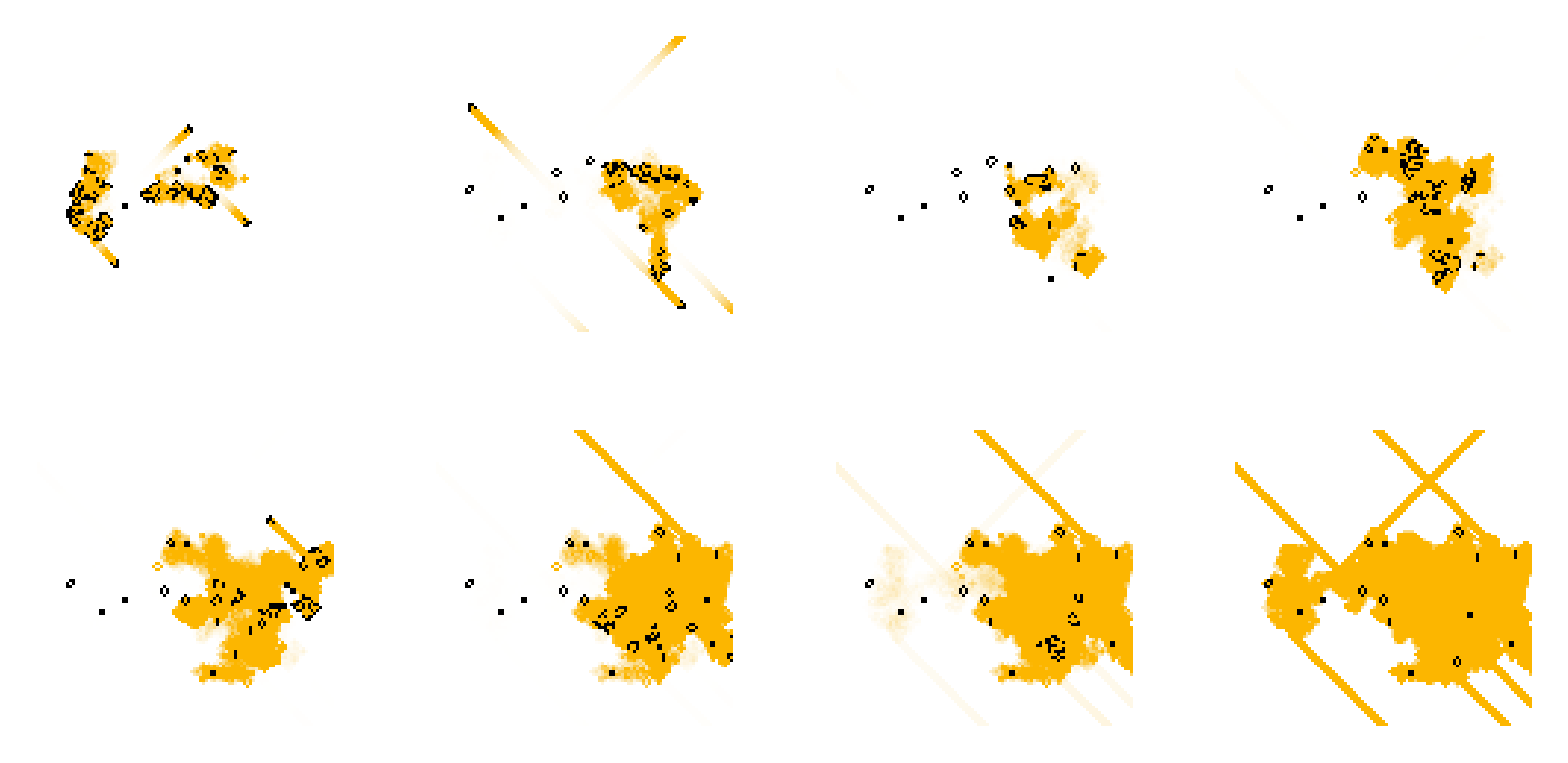

```mathematica
GraphicsGrid[Partition[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{#,{-50,50},{-50,50}},Mesh->(#<100),"Decay"-><|150->.9,300->.95,450-> .95, 600->.98,750->.985,900->.99,1050-> .995,  1200->.999|>[#]]&/@{150,300,450,600,750,900,1050,1200}, 4]]
```

```mathematica
GraphicsRow[{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},#,Mesh->True, MeshStyle->GrayLevel[0,.15],Lighting->]&/@{150,300,1120}]
```

```mathematica
GraphicsRow[{{"[◼]", "CellularAutomatonSpacetimePlot2"}}["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},#,
"Decay"->.99,Mesh->(#<101),ColorRules->{-1->Black, x_/; x!=-1:>Blend[{{0,RGBColor[1., 1., 1.]},{.01,RGBColor[1., 0.9461, 0.7000000000000001]},{.3,RGBColor[1., 0.66, 0.]},{.5,RGBColor[0.98, 0.42, 0.04]},{.8,RGBColor[0.7000000000000001, 0., 0.37800000000000006]}},x]}]&/@{150,300,600,900}]
```

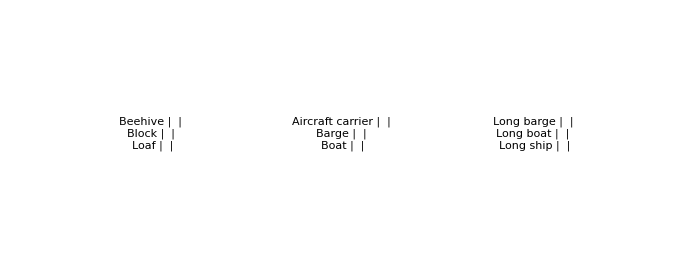

```mathematica
GraphicsRow[Grid[{{"[◼]", "CellularAutomatonCompositePlot"}}[#,{{"Trails",10,.9}->{Automatic, 60},{"3D",6}->{60, 60}}]&/@#,Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{2->1, 2.5}]&/@ Partition[ResourceData["LifeWiki Dataset 2025"]/@{"Beehive","Block","Loaf","Aircraft carrier","Barge","Boat","Long barge","Long boat","Long ship"},3], Spacings->{38, Automatic}]
```

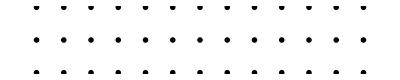

```mathematica
GraphicsGrid[ArrayPlot[ArrayPad[#,{1,1}],Mesh->True,MeshStyle->Opacity[.1],ImageSize->50]&/@CellularAutomaton["GameOfLife",{ResourceData["LifeWiki Dataset 2025"][#]["MatrixData"],0},12]&/@{"Blinker","Traffic light","Figure eight"},Spacings->{10,20}]
```

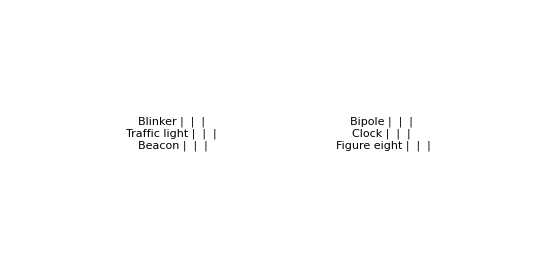

```mathematica
GraphicsRow[Grid[{{"[◼]", "CellularAutomatonCompositePlot"}}[#,{"Static"->{60, 60},{"Trails",10,.9}->{60, 60},{"3D",6}->{60, 60}}]&/@#,Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{1}, 2.5}]&/@Partition[ResourceData["LifeWiki Dataset 2025"]/@{"Blinker","Traffic light","Beacon","Bipole","Clock","Figure eight","Figure eight"},3],Spacings->30]
```

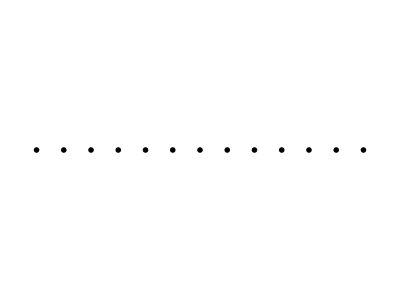

```mathematica
GraphicsGrid[ArrayPlot[ArrayPad[#,{1,1}],Mesh->True,MeshStyle->Opacity[.1],ImageSize->50]&/@CellularAutomaton["GameOfLife",{ResourceData["LifeWiki Dataset 2025"][#]["MatrixData"],0},12]&/@{"Glider"},Spacings->{10,0}]
```

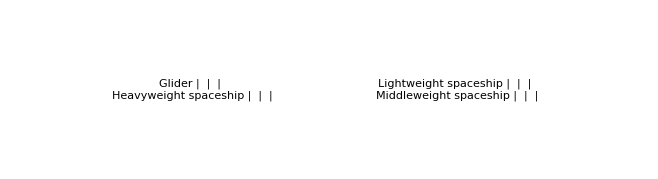

```mathematica
GraphicsRow[Grid[{{"[◼]", "CellularAutomatonCompositePlot"}}[#,{"Static"->{60, 60},{"Trails",20,.9}->{100, 60},{"3D",8}->{60, 60}},"Margin"-> 1, "Transform"-> If[# === "Glider", Identity, (Reverse/@#&)]]&/@#,Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{1}, 2.5}]&/@Partition[ResourceData["LifeWiki Dataset 2025"]/@{"Glider","Heavyweight spaceship","Lightweight spaceship","Middleweight spaceship"},2],Spacings->30]
```

```mathematica
GraphicsGrid[With[{ca={{"[◼]", "PatternElements"}}[CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{{{1104}}}]]},{KeyValueMap[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#,0},8,ImageSize->50],Text[StringJoin[ToString[#2],"×"]],Top]&,ca],KeyValueMap[{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{#,0},14,ImageSize->{Automatic,100}]&,ca]}]]
```

```mathematica
AnimatedImage[Rasterize[ArrayPlot[CellularAutomaton["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Gosper glider gun"]["MatrixData"], 0}, {{{#}}, {-1, 25}, {-2, 45}}], 
Mesh->True,MeshStyle->Opacity[0.1],ImageSize->250,PlotRangePadding->.15]]&/@Range[75,104]]
```

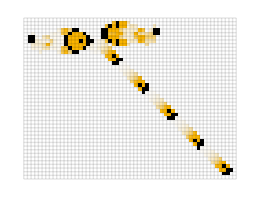
-Graphics--Graphics3D--Graphics-

```mathematica
Row[{{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Gosper glider gun"]["MatrixData"], 0},150,ImageSize->260],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Gosper glider gun"]["MatrixData"], 0},100,ImageSize->140,ViewPoint->{-2.198487002413733,-2.3413385931086927,1.0652645176845457}],{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Gosper glider gun"]["MatrixData"], 0},250,"Decay"->.99,ImageSize->95,Mesh->None]},Spacer[30]]
```

```mathematica
GraphicsRow[{{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Period-15 glider gun"]["MatrixData"], 0},150,ImageSize->{Automatic, 260},"Decay"->.7],
{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Period-15 glider gun"]["MatrixData"], 0},100,ImageSize->{Automatic, 280},ViewPoint->{3.0373115164062576,-1.449486231706877,0.35175050305311767}(*, ImageSize-> {75, Automatic}*)],{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Period-15 glider gun"]["MatrixData"], 0},250,"Decay"->.99,ImageSize->{Automatic, 280},Mesh->None]},Spacings->35]
```

-Graphics-

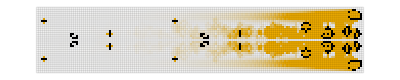

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{Reverse/@Transpose[ResourceData["LifeWiki Dataset 2025"]["Puffer 1"]["MatrixData"]], 0},300,"Decay"->.97]
```

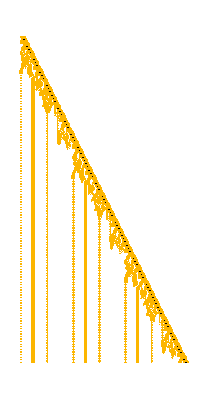

```mathematica
GraphicsRow[Join[{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Puffer 1"]["MatrixData"],0},#,ViewPoint->{2.8443765188744194,-1.8320647919555706,0.055324650497145265},ImageSize->{Automatic,340}]&/@{100,300},{{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{Reverse/@Transpose[ResourceData["LifeWiki Dataset 2025"]["Puffer 1"]["MatrixData"]], 0},400,ImageSize->{Automatic,320},"Decay"->.97,Mesh->None]}],Spacings->30]
```

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Breeder 1"]["MatrixData"],0},300,Mesh->None]
```

-Graphics-

```mathematica
{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Breeder 1"]["MatrixData"],0},300,ViewPoint->{1.1216495614439776,-2.5887426117046104,1.8682381945719146}]
```

```mathematica
{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Breeder 1"]["MatrixData"],0},300,Mesh->None,"Decay"->.995]
```

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Breeder 1"]["MatrixData"],0},1000,Mesh->None]
```

```mathematica
GraphicsRow[Join[{ArrayPlot[ArrayPad[ResourceData["LifeWiki Dataset 2025"]["Spacefiller 1"]["MatrixData"],1],Mesh->True,MeshStyle->Opacity[.1]]},Map[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Spacefiller 1"]["MatrixData"],0},#,Mesh->True,MeshStyle->Opacity[.05]]&,{20,50}]],Spacings->10]
```

-Graphics-

```mathematica
GraphicsRow[{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Spacefiller 1"]["MatrixData"],0},#,Lighting->]&/@{20,50}]
```

-Graphics-

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{SparseArray[…],0},1600,Mesh->None,"Decay"->.97, FrameTicks->{False,Table[{60*Prime[i] - 115, Prime[i]}, {i, 1,6}]}]
```

```mathematica
Show[{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{SparseArray[…],0},1600,Mesh->None,"Decay"->.99],TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],FrameTicks->{Table[{60*Prime[i] - 115, Prime[i]}, {i, 1,5}], False, False, False}]
```

```mathematica
GraphicsGrid[
Function[row, Take[row, #]&/@ {{1, 13}, {14, 27}, {28, -1}}][KeyValueMap[Labeled[ArrayPlot[ArrayPad[#,1],Mesh->True,MeshStyle->Opacity[.1],ImageSize->{Automatic, 30}],Text[Style[StringTemplate["``×"][#2], 11]],Top]&,ReverseSort@{{"[◼]", "PatternElements"}}[SparseArray[…]]]](*, Spacings->{12, Automatic}*)]
```

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["p5760 unit Life cell"]["MatrixData"],0},200,Mesh->None,"Decay"->.95]
```

-Graphics-

```mathematica
GraphicsRow[{GraphicsGrid[Partition[Table[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Glider pusher"]["MatrixData"],0},{4 n,{-2,25},{-2,28}},"Decay"->.93],{n,2,9}],4], ImageSize-> {Automatic, 200}],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Glider pusher"]["MatrixData"],0},40, Mesh->True, MeshStyle->GrayLevel[0,.15],Lighting->,ViewPoint->{2.088321875639556,-2.6284768080224388,0.42428930391120906},ImageSize->{Automatic,200}, PlotRangePadding->None]}]
```

-Graphics-

```mathematica
Row[{GraphicsRow[Table[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{Transpose@{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,1,1,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0}},0},t,"Decay"->.9],{t,2,32,4}],ImageSize->450],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{Transpose@{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,1,1,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0}},0},32, Mesh->True, MeshStyle->GrayLevel[0,.15],Lighting->,ViewPoint->{3.146,-1.095,0.593},ViewVertical->{-0.412,0.066,0.908},ImageSize->115]},Spacer[20]]
```

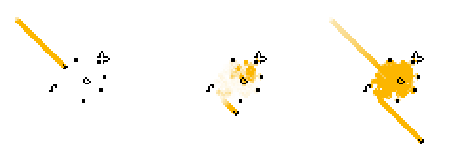
-Graphics--Graphics3D-

```mathematica
Row[{GraphicsRow[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Bandersnatch"]["MatrixData"],0},{#,{0,70},{0,60}},Mesh->None,"Decay"->#2]&@@@{{100,.99},{200,.9},{260,.99}},ImageSize->460],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Bandersnatch"]["MatrixData"],0},{{80,220}},ImageSize->{102,Automatic}]},Spacer[20]]
```

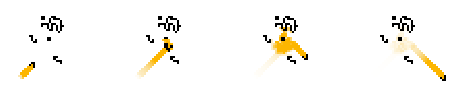
-Graphics--Graphics3D-

```mathematica
Row[{GraphicsRow[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{SparseArray[…],0},{#,{0,35},{0,40}},Mesh->None,"Decay"->#2]&@@@{{20,.95},{60,.95},{100,.95},{140,.95}},ImageSize->460],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Snark"]["MatrixData"],0},90,Mesh->True,MeshStyle->Opacity[.1],ViewPoint->{-3.1109281250378347,-0.02451443444705201,1.330986567682907},ImageSize->72]},Spacer[20]]
```

```mathematica
Row[{GraphicsRow[Table[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{Transpose[SparseArray[…]],0},t,Mesh->None],{t,80,160,20}],ImageSize->415],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{SparseArray[…],0},{{30,160+30}},ImageSize->115]},Spacer[20]]
```

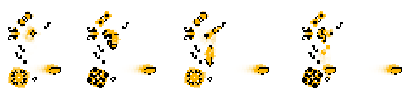
-Graphics--Graphics3D-

```mathematica
Row[{GraphicsRow[Table[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{SparseArray[…],0},t,Mesh->None,ImageSize->{Automatic,160}],{t,80,150,20}],ImageSize->415],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{SparseArray[…],0},{{78,160+30}},ImageSize->220]},Spacer[5]]
```

## The Arc of Progress

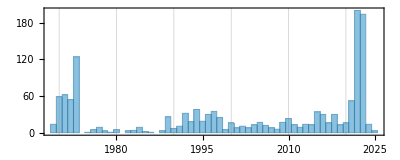

```mathematica
Histogram[Values[#Year&/@ResourceData["LifeWiki Dataset 2025"]],{1},Frame->True,TicksStyle->GrayLevel[.25] ,FrameTicksStyle->GrayLevel[.25],AspectRatio->.4,FrameLabel->{"year",None},GridLines->{Range[1970,2020,10],None}, ChartStyle->Directive[Opacity[.6,ColorData["DefaultPlotColors"][1]],EdgeForm[Darker[ColorData["DefaultPlotColors"][1]]]]]
```

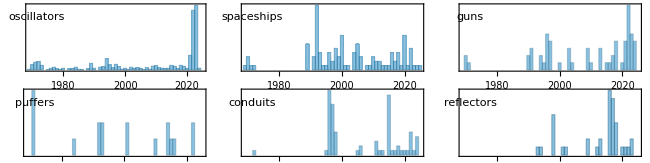

```mathematica
GraphicsGrid[Partition[KeyValueMap[Histogram[#2,{1},PlotRange->{{1969,2025},Automatic},Frame->True,FrameTicks->{Automatic,None},TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],AspectRatio->.3,ImageSize->200,PlotRangePadding->{Automatic,{0,Scaled[.15]}},Epilog->Style[Text[ToLowerCase[Pluralize@#1],Scaled[{.06,.8}],{-1,0}],11],
ChartStyle->Directive[Opacity[.6,ColorData["DefaultPlotColors"][1]],EdgeForm[Darker[ColorData["DefaultPlotColors"][1]]]]]&,],3],ImageSize->650,Spacings->{3,7}]
```

```mathematica
iys = ;
```

```mathematica
counts = {StringCount[#,"discover"|"use"],StringCount[#,"construct"]}&/@ Most@*Reverse@*Most@iys;
```

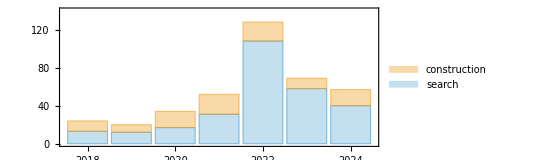

```mathematica
BarChart[counts, ChartLayout->"Stacked",PlotRange->{{0.5,7.5},{0,140}},ChartLegends->{"search","construction"},AspectRatio->.4,Frame->True, FrameTicks->{{Automatic,None},{Transpose[{Range[1,7],Riffle[Range[2018,2025,2],None]}],Automatic}}, ChartStyle->{
Directive[Opacity[.3,ColorData["DefaultPlotColors"][1]],EdgeForm[{Thick,ColorData["DefaultPlotColors"][1]}]], Directive[Opacity[.4,ColorData["DefaultPlotColors"][2]],EdgeForm[{Thick,ColorData["DefaultPlotColors"][2]}]]}, BarSpacing->.1]
```

```mathematica
GraphicsRow[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{#,{-10,10},{-30,17}},Mesh->False,"Decay"->.7]&/@{70,74,83}]
```

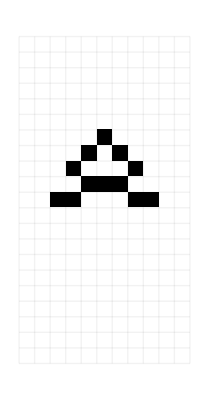
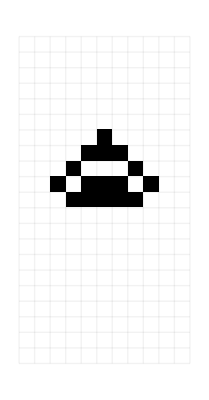
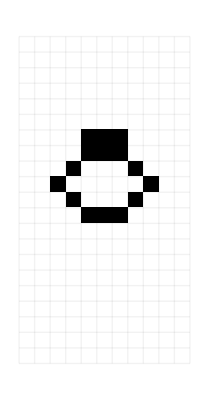
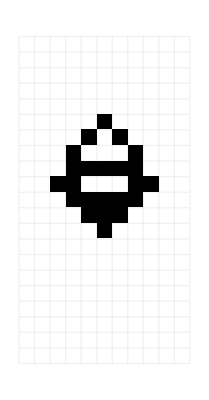
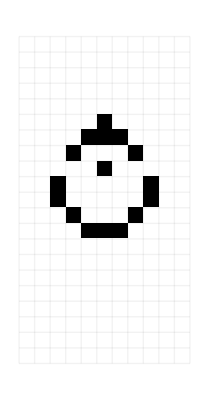
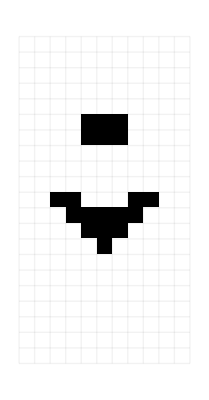
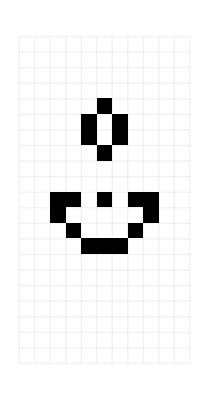
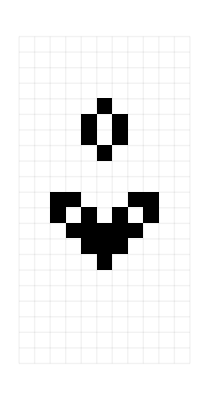

```mathematica
GraphicsGrid[Partition[ArrayPlot[ArrayPad[#,1],Mesh->True,MeshStyle->Opacity[.05]]&/@CellularAutomaton["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Queen bee"]["MatrixData"],0},36],18]]
```

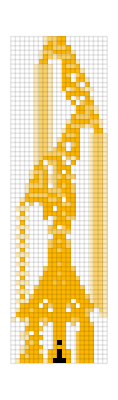

```mathematica
GraphicsRow[{{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Queen bee"]["MatrixData"],0},70,ViewPoint->{3.1309623028268923,0.5424157801164059,1.1631251780258365}],{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{Transpose@ResourceData["LifeWiki Dataset 2025"]["Queen bee"]["MatrixData"],0},70,"Decay"->.9]}]
```

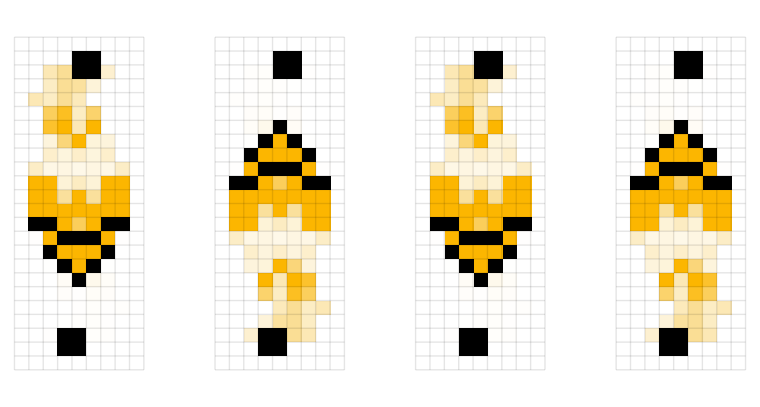

```mathematica
GraphicsRow[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{Transpose@ResourceData["LifeWiki Dataset 2025"]["Queen bee shuttle"]["MatrixData"], 0},#,ImageSize->260]&/@Range[45,90,15],Spacings->40]
```

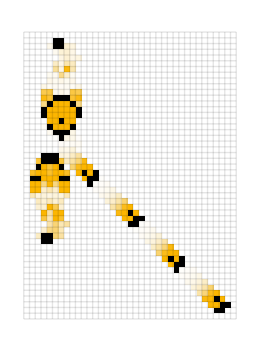

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{Transpose@ResourceData["LifeWiki Dataset 2025"]["Gosper glider gun"]["MatrixData"], 0},120,ImageSize->260]
```

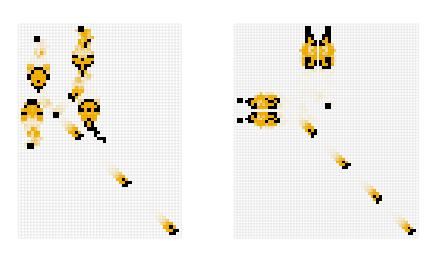

```mathematica
GraphicsRow[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{Transpose@ResourceData["LifeWiki Dataset 2025"][#]["MatrixData"], 0},150,MeshStyle->Opacity[.05],ImageSize->{Automatic,250}]&/@{"Period-60 glider gun","New gun 1"}]
```

```mathematica
GraphicsRow[ArrayPlot[ArrayPad[#,1],Mesh->True,MeshStyle->Opacity[.1]]&/@CellularAutomaton["GameOfLife",{SparseArray[…],0},13]]
```

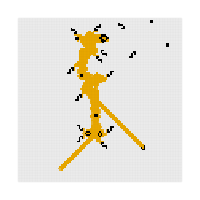

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Silver's reflector"]["MatrixData"],0},{300,{0,100},{100,200}},"Decay"->.999,MeshStyle->Opacity[.05], ImageSize-> {200, Automatic}]
```

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{SparseArray[…],0},{100,{0,35},{0,40}},MeshStyle->Opacity[.1],"Decay"->.98]
```

```mathematica
GraphicsRow[Append[ArrayPlot[ArrayPad[#,2],Mesh->True,MeshStyle->Opacity[.1]]&/@CellularAutomaton["GameOfLife",{SparseArray[…],0},6][[{1,7}]],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{SparseArray[…],0},30,ViewPoint->{-1.5100606938664856,-2.9431988487688194,0.712248016806903}]]]
```

```mathematica
GraphicsRow[Append[ArrayPlot[ArrayPad[#,2],Mesh->True,MeshStyle->Opacity[.05]]&/@CellularAutomaton["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Sir Robin"]["MatrixData"],0},12][[{5,11}]],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Sir Robin"]["MatrixData"],0},30,ViewPoint->{-1.5100606938664856,-2.9431988487688194,0.712248016806903}]]]
```

-Graphics-

```mathematica
GraphicsRow[{ArrayPlot[ArrayPad[ResourceData["LifeWiki Dataset 2025"]["R64"]["MatrixData"],{{1,1},{11,1}}],Mesh->True,MeshStyle->Opacity[.1]],{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["R64"]["MatrixData"],0},64,MeshStyle->Opacity[.1],"Decay"->.95]}]
```

-Graphics-

```mathematica
GraphicsRow[{ArrayPlot[ArrayPad[ResourceData["LifeWiki Dataset 2025"]["RF28B"]["MatrixData"],{{1,5},{2,3}}],Mesh->True,MeshStyle->Opacity[.1]],{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["RF28B"]["MatrixData"],0},28,MeshStyle->Opacity[.1],"Decay"->.6]},Spacings->30]
```

-Graphics-

```mathematica
b = 10;
ts={1,2,3,4,5,6,7,8,9,10,20,30,40,50,60,70,80,90,100};
logCoords=Rescale[Log[b, ts],{Log[b, 1],Log[b, 100]},{100,0}];
```

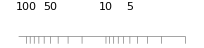
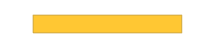
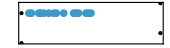
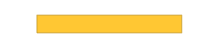
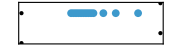
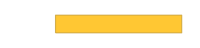
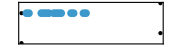
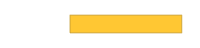
-Graphics- |  | -Graphics-
-Graphics- | David Buckingham | -Graphics-
-Graphics- | Dean Hickerson | -Graphics-
-Graphics- | Robert Wainwright | -Graphics-
-Graphics- | Noam Elkies | -Graphics-
-Graphics- | Mitchell Riley | -Graphics-
-Graphics- | Matthias Merzenich | -Graphics-
-Graphics- | Tanner Jacobi | -Graphics-
-Graphics- | John Conway | -Graphics-
-Graphics- | Hartmut Holzwart | -Graphics-
-Graphics- | David Bell | -Graphics-
-Graphics- | Nicolay Beluchenko | -Graphics-
-Graphics- | Nico Brown | -Graphics-
-Graphics- | Jason Summers | -Graphics-
-Graphics- | Bill Gosper | -Graphics-
-Graphics- | Paul Callahan | -Graphics-
-Graphics- | JHC group | -Graphics-
-Graphics- | Charity Engine | -Graphics-
-Graphics- | Achim Flammenkamp | -Graphics-
-Graphics- | MIT group | -Graphics-
-Graphics- | David Raucci | -Graphics-
-Graphics- | Adam P. Goucher | -Graphics-
-Graphics- | Paul Tooke | -Graphics-
-Graphics- | Luke Kiernan | -Graphics-
-Graphics- | Tim Coe | -Graphics-
-Graphics- | Michael Simkin | -Graphics-
-Graphics- | Stephen Silver | -Graphics-
-Graphics- | Scot Ellison | -Graphics-
-Graphics- | Karel Suhajda | -Graphics-
-Graphics- | Josh Ball | -Graphics-
-Graphics- | Dongook Lee | -Graphics-
-Graphics- | Dave Greene | -Graphics-
-Graphics- | Chris Cain | -Graphics-
-Graphics- | Martin Grant | -Graphics-
-Graphics- | Ivan Fomichev | -Graphics-
-Graphics- | iNoMed | -Graphics-
-Graphics- | Dietrich Leithner | -Graphics-
-Graphics- | Charles Corderman | -Graphics-
-Graphics- | Rich Schroeppel | -Graphics-
-Graphics- | carybe | -Graphics-
-Graphics- | Simon Norton | -Graphics-
-Graphics- | Simon Ekström | -Graphics-
-Graphics- | Sergey Petrov | -Graphics-
-Graphics- | Rob Liston | -Graphics-
-Graphics- | Nick Gotts | -Graphics-
-Graphics- | Mike Playle | -Graphics-
-Graphics- | Mark Niemiec | -Graphics-
-Graphics- | Luka Okanishi | -Graphics-
-Graphics- | Goldtiger997 | -Graphics-
-Graphics- | Gabriel Nivasch | -Graphics-
-Graphics- | David Eppstein | -Graphics-

```mathematica
discoveries=Take[SortBy[GroupBy[
Values[Values/@Select[,KeyExistsQ[#,"Discovered by"]&&StringQ[#[["Discovered by"]]]&][[All,{"Discovered by","Year of discovery"}]]],First->Last],Length],-50];
Grid[{{Graphics[
scale = 1.25;Join[{Gray,Thickness[.0025],Line[{{-5*scale,0},{100*scale,0}}],Line[{{#*scale,0},{#*scale,-1.5}}]&/@logCoords},{Black},Table[Text[ToString[i],{Rescale[Log[b, i],{Log[b, 1],Log[b, 100]},{100*scale,0}],6}],{i,{5,10,50,100}}]],ImageSize->{204,Automatic}]
,Null,Graphics[{},AspectRatio->.06,PlotRange->{{1969,2025},Automatic},
ImageSize->170,Axes->{True,False},AxesStyle->White,
TicksStyle->White,LabelStyle->GrayLevel[0.25],ImageMargins->{{0,0},{5,0}}]}} ~Join~
Map[{
Item[BarChart[{2.75Length[#[[2]]]^.35}+1, BarOrigin->Right,AspectRatio->.05, ChartStyle->EdgeForm[Hue[0.12091505713081323, 0.8000000035401837, 0.76]],
PlotRangePadding->{.05, .0},Axes->False,PlotRange->{{0,15},{0,2}},ImageSize->200],Alignment->Top],
Item[Style[#[[1]],"Label"],Alignment->Top],
TimelinePlot[DeleteDuplicates[DeleteMissing[#[[2]]]],Axes->False,
AspectRatio->.06,PlotRange->{{1969},{2025}},ImageSize->170,PlotMarkers->{Automatic,8},
Frame->{{False,False},{True,False}},FrameTicks->False,FrameStyle->GrayLevel[.85]]
}&,Reverse[Normal[discoveries]]],
Alignment->{Right,Bottom},Spacings->{.5,0}]
```

## The Example of Oscillators

```mathematica
progress =Module[{sorted = SortBy[Select[Values[ResourceData["LifeWiki Dataset 2025"]],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 30}]];
```

```mathematica
ListPlot[
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress[[All,1]]], PlotStyle->Directive[Red, PointSize[.01]],PlotRange->{{1969, 1981}, {1, 30}},Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@Select[progress[[All, 1]],#Year<1981&]}), PlotRange->{{1969, 1981}, {0, 30}}, AspectRatio->.4, Frame-> True, TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],PlotRangePadding->{0, {0, 1.5}}]
```

-Graphics-

```mathematica
progress =Module[{sorted = SortBy[Select[Values[ResourceData["LifeWiki Dataset 2025"]],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 30}]];
```

```mathematica
ListPlot[
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress[[All,1]]], PlotStyle->Directive[Red, PointSize[.01]], PlotRange->{{1969, 2025}, {1, 30}},Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, 1]]}), PlotRange->{{1969, 2025}, {0, 30}}, AspectRatio->.4, Frame-> True, TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],PlotRangePadding->{0, {0, 1.5}}]
```

-Graphics-

```mathematica
ListStepPlot[With[{ys={#Period,#Year}&/@With[{o=Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&]},Table[First@MinimalBy[Select[o,#Period===p&],#Year&,1],{p,2,60}]]},Table[{y,Count[Last/@ys,x_/;x<=y]},{y,1969,2025}]],Frame->True,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],AspectRatio->.4,Filling->Axis,FrameLabel->{Automatic,"number of periods found"}]
```

-Graphics-

```mathematica
progress =Module[{sorted = SortBy[Select[Values[ResourceData["LifeWiki Dataset 2025"]],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 30}]];
```

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.01]], PlotRange->{{1969, 2025}, {1, 30}},Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, -1]]}), PlotRange->{{1969, 2025}, {0, 30}}, AspectRatio->.4, Frame-> True, TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],PlotRangePadding->{0, {0, 1.5}}]
```

-Graphics-

```mathematica
progress2 =DeleteCases[Module[{curr, weightsovertime,improvements,locs, sorted},
Table[
sorted = Catenate[
ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@ 
GatherBy[SortBy[Select[Select[Values[ResourceData["LifeWiki Dataset 2025"]],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==i&],#Year&], #Year&]
];
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 100}]], {}];
```

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress2, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.0075]], PlotRange->{{1969, 2025}, {1, 100}}, Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress2[[All, -1]]}), PlotRange->{{1969, 2025}, {0, 100}}, AspectRatio->.4, Frame-> True,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25], PlotRangePadding->{0, {0,3}}]
```

-Graphics-

```mathematica
Quiet@ListLinePlot[MapIndexed[Labeled[Callout[Style[{#Year,Times@@Dimensions[#MatrixData]}],ArrayPlot[ArrayPad[#MatrixData,1],ImageSize->Tiny], LabelVisibility->Automatic]&/@#, If[Times@@Dimensions[#[[1, "MatrixData"]]] >= 1900, First[#2], None],Left]&,Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[ResourceData["LifeWiki Dataset 2025"]],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
SortBy[Select[Select[Values[ResourceData["LifeWiki Dataset 2025"]],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]],{i,2,50}]],PlotStyle->PointSize[.01],PlotRange->All,AspectRatio->.4,Frame->True,
TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],FrameLabel->{None,"area"},PlotRangePadding->{{.2,.2},Automatic}]
```

-Graphics-

```mathematica
ListLinePlot3D[MapIndexed[Callout[{#Year,#Period,Times@@Dimensions[#MatrixData]},If[First[#2] == 1, ArrayPlot[ArrayPad[#MatrixData,1],ImageSize->Tiny], None]]&,#]&/@Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[ResourceData["LifeWiki Dataset 2025"]],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
SortBy[Select[Select[Values[ResourceData["LifeWiki Dataset 2025"]],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]],{i,2,50}],PlotRange->All,AxesLabel->{None,"period","area"},BoxRatios->{2,1,.6},Filling->Axis,ScalingFunctions->{None,None,{Sqrt,#^2&}}, PlotMarkers->{"Point", Large}, PlotStyle->PointSize[.001]]
```

-Graphics3D-

```mathematica
Row[Column[Table[Module[{weightsovertime,improvements,locs,p=i,byyear},byyear=Catenate[ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@GatherBy[SortBy[Select[Select[Values[ResourceData["LifeWiki Dataset 2025"]],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&],#Year&]];
weightsovertime=Times@@Dimensions[#MatrixData]&/@byyear;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[Column[{GraphicsRow[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},#Period,ImageSize->3 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]],Text[Style[#Year,9,GrayLevel[.25]]],BaselinePosition->Top]&/@byyear[[locs]]],NumberLinePlot[Callout[#Year,#Year]&/@SortBy[Select[Select[Values[ResourceData["LifeWiki Dataset 2025"]],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]],Axes->None,PlotRange->{1968,2025}]}],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}]&/@{Range[2,12],Range[13,21]},Spacer[15]]
```

-Graphics-
-Graphics-period 2  
-Graphics-
-Graphics-period 3  
-Graphics-
-Graphics-period 4  
-Graphics-
-Graphics-period 5  
-Graphics-
-Graphics-period 6  
-Graphics-
-Graphics-period 7  
-Graphics-
-Graphics-period 8  
-Graphics-
-Graphics-period 9  
-Graphics-
-Graphics-period 10  
-Graphics-
-Graphics-period 11  
-Graphics-
-Graphics-period 12  -Graphics-
-Graphics-period 13  
-Graphics-
-Graphics-period 14  
-Graphics-
-Graphics-period 15  
-Graphics-
-Graphics-period 16  
-Graphics-
-Graphics-period 17  
-Graphics-
-Graphics-period 18  
-Graphics-
-Graphics-period 19  
-Graphics-
-Graphics-period 20  
-Graphics-
-Graphics-period 21

```mathematica
GraphicsGrid[Partition[ArrayPlot/@CellularAutomaton["GameOfLife",{{Join[Table[1,5],{0},Table[1,5]]},0},30],15]]
```

```mathematica
GraphicsRow[{GraphicsRow[ArrayPlot[ArrayPad[#,1],Mesh->True,MeshStyle->Opacity[.1]]&/@CellularAutomaton["GameOfLife",{{{0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,1,0,0,0,0},{1,1,0,1,0,0,0,0,1,0,0,0},{1,1,0,1,0,1,1,0,1,0,0,0},{0,0,0,1,0,1,1,0,1,0,1,1},{0,0,0,1,0,0,0,0,1,0,1,1},{0,0,0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0}},0},4]],GraphicsRow[ArrayPlot[ArrayPad[#,1],Mesh->True,MeshStyle->Opacity[.1]]&/@CellularAutomaton["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Pinwheel"]["MatrixData"],0},4]]}]
```

-Graphics-

```mathematica
GraphicsRow[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"][#]["MatrixData"],0},ResourceData["LifeWiki Dataset 2025"][#]["Period"]],Text[Style[StringTemplate["period ``"][ResourceData["LifeWiki Dataset 2025"][#]["Period"]],GrayLevel[0.25]]]]&/@{"Unix","Worker bee","Dinner table"},Spacings->20]
```

-Graphics-

```mathematica
GraphicsRow[{GraphicsRow[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{First[#],0},Last[#],ImageSize->6Last[Dimensions[First[#]]]],Text[Style[StringTemplate["period ``"][Last[#]],GrayLevel[0.25]]]]&/@{{Last[CellularAutomaton["GameOfLife",{Reverse/@ResourceData["LifeWiki Dataset 2025"]["Mold"]["MatrixData"],0},9]],4},
{Last[CellularAutomaton["GameOfLife",{Reverse/@Transpose[ResourceData["LifeWiki Dataset 2025"]["Fire-spitting"]["MatrixData"]],0},9]],3},
{Last[CellularAutomaton["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Mold on fire-spitting"]["MatrixData"],0},9]],12}}],GraphicsRow[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{First[#],0},Last[#],ImageSize->6Last[Dimensions[First[#]]]],Text[StringTemplate["period ``"][Last[#]]]]&/@{{Reverse/@Last[CellularAutomaton["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Caterer"]["MatrixData"],0},8]],3},{Last[CellularAutomaton["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Figure eight"]["MatrixData"],0},7]],8},{Last[CellularAutomaton["GameOfLife",{Transpose[ImportString["x=6,y=18,rule=B3/S23
bo$obo2$2bo$b2o$b5o$b2ob2o$2bo5$3o$3o$3o$3b3o$3b3o$3b3o!","RLE"]],0},6]],24}}]},Spacings->40]
```

-Graphics-

```mathematica
Module[{p3=SortBy[Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Oscillator"&&#Period==3&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],improvements},improvements=Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]];
Row[Values[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},6,MeshStyle->Opacity[.05],ImageSize->11 Sqrt[1+Last[Dimensions[#MatrixData]]],Frame->MemberQ[improvements,#],FrameStyle->Directive[Red,Thickness[.05]]],Text[Style[#Year,9,GrayLevel[0.25]]]]&/@p3],Spacer[1]]]
```

-Graphics-1970-Graphics-1970-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1973-Graphics-1973-Graphics-1973-Graphics-1977-Graphics-1982-Graphics-1985-Graphics-1988-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1990-Graphics-1993-Graphics-1993-Graphics-1993-Graphics-1993-Graphics-1994-Graphics-1997-Graphics-2003-Graphics-2012-Graphics-2017-Graphics-2018-Graphics-2021-Graphics-2022

```mathematica
GraphicsRow[{{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["p67 Herschel loop"]["MatrixData"],0},67,"Decay"->.95,Mesh->None,ImageSize->{Automatic,250}],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["p67 Herschel loop"]["MatrixData"],0},2 67,ViewPoint->{2.716721076863372,-1.995782064969705,0.2937354926997763},ImageSize->{Automatic,280}],{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["p67 Herschel loop"]["MatrixData"],0},67 2,"Decay"->.9,Mesh->None,ImageSize->{Automatic,280}]},Spacings->50]
```

-Graphics-

```mathematica
Module[{p3=Drop[SortBy[Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Oscillator"&&#Period==16&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],{-2}],improvements},improvements=Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]];
Row[Values[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},16,MeshStyle->Opacity[.07],ImageSize->14 Sqrt[1+Last[Dimensions[#MatrixData]]],Frame->MemberQ[improvements,#],FrameStyle->Directive[Red,Thickness[.05]]],Text[Style[#Year,9,GrayLevel[0.25]]]]&/@p3],Spacer[1]]]
```

-Graphics-1983-Graphics-1984-Graphics-1994-Graphics-1994-Graphics-1994-Graphics-2016-Graphics-2018-Graphics-2020-Graphics-2022-Graphics-2022-Graphics-2022-Graphics-2023

```mathematica
GraphicsRow[Values[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#["MatrixData"],0},57,"Decay"->.9,MeshStyle->Opacity[.1],Mesh->Length[#["MatrixData"]]<50,ImageSize->50Length[#["MatrixData"]]^.2],Text[Style[#Year,9,GrayLevel[0.25]]]]&/@Take[Quiet[Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Oscillator"&&#Period===57&]],2]],Spacings->40]
```

-Graphics-

## Modularity

```mathematica
mmm=ArrayPad[Normal[ResourceData["LifeWiki Dataset 2025"]["Worker bee"]["MatrixData"]],1];
```

```mathematica
GraphicsRow[With[{g=NearestNeighborGraph[Position[Transpose[
Reverse[#]],1], {All,2Sqrt[2]}]},ArrayPlot[#,Mesh->True,MeshStyle->Opacity[.1],ColorRules->{1->Hue[0.56, 0.29, 0.73]},Epilog->Style[Line[List@@#-.5]&/@EdgeList[Graph[g,VertexCoordinates->Thread[VertexList[g]->VertexList[g]]]],AbsoluteThickness[1.5],Red]]]&/@CellularAutomaton["GameOfLife",mmm,2]]
```

-Graphics-

```mathematica
Row[{GraphicsColumn[With[{g=NearestNeighborGraph[Position[Transpose[
Reverse[#]],1], {All,2Sqrt[2]}]},ArrayPlot[#,Mesh->True,MeshStyle->Opacity[.1],ColorRules->{1->Hue[0.56, 0.29, 0.73]},Epilog->Style[Line[List@@#-.5]&/@EdgeList[Graph[g,VertexCoordinates->Thread[VertexList[g]->VertexList[g]]]],AbsoluteThickness[1.5],Red]]]&/@CellularAutomaton["GameOfLife", {ResourceData["LifeWiki Dataset 2025"]["Worker bee"]["MatrixData"], 0}, 9], ImageSize->60],(*Rasterize[*)GraphPlot[{{"[◼]", "PatternsLayeredGraph"}}[ResourceData["LifeWiki Dataset 2025"]["Worker bee"], Automatic, "VertexSizeFunction"-> (4Dimensions[#]&), ImageSize-> 240], PlotRangePadding->{Automatic, {0,1}}](*]*)
}, Spacer[10]]
```

-Graphics--Graphics-

```mathematica
{{"[◼]", "BoundingBoxLayeredGraph"}}[ResourceData["LifeWiki Dataset 2025"]["Worker bee"]]
```

-Graphics-

```mathematica
allimps = Table[Module[{p3=SortBy[Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Oscillator"&&#Period==i&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],improvements},improvements=DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]]],{i, 2,60}];
```

```mathematica
Grid[{
Column[{
{{"[◼]", "BoundingBoxLayeredGraph"}}[#, Automatic(*, ImageSize->{125, 210} *)(*PlotRange-> {{-15, 8}, Automatic}*)],{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},16, ImageSize->{90, 75}
(*6 Sqrt[Last[Dimensions[#MatrixData]]]*)(*{75, 50}*)]}, Spacings->{0,1.5},Alignment->Center] &/@SortBy[allimps[[15]],#Year&],
Style[Text[#Year], 11,GrayLevel[0.25]]&/@SortBy[allimps[[15]],#Year&]
},(*Frame->{None, Automatic},*)FrameStyle->Opacity[.2],Dividers->{All,False}, Alignment->Center, Spacings->{1, {1.5,.2}}]
```

-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
1983 | 1994 | 1994 | 2016 | 2020

```mathematica
Grid[Transpose[Values[{GraphPlot[{{"[◼]", "BoundingBoxLayeredGraph"}}[#,Automatic], ImageSize->{Automatic, 145}],
Rotate[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},16,ImageSize->(*10 Sqrt[Last[Dimensions[#MatrixData]]],*)If[#Name ==="p30rpentominohassler2" , {Automatic, UpTo[75]}, {UpTo[75], Automatic}],MeshStyle->Opacity[(.5/(Times@@Dimensions[#MatrixData])^.4)]], If[#Name ==="p30rpentominohassler2", 0, Pi/2]] ,Column[Style[Text[#], 11,GrayLevel[0.25]]&/@{#Year,Round[N[VertexCount[{{"[◼]", "BoundingBoxLayeredGraph"}}[#,#Period-1]]/#Period,3], .1]}]}&/@SortBy[Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Oscillator"&&#Period==30&]//Quiet,#Year&]]],(*Spacer[2],*)Dividers->{All, False},FrameStyle->Opacity[.2], Alignment->Center]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1970
3.2 | 1980
5.1 | 1984
9.6 | 1985
16.3 | 1995
2.8 | 2022
9.5 | 2022
3.1 | 2022
11.1 | 2023
3.7

```mathematica
allimps = Table[Module[{p3=SortBy[Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Oscillator"&&#Period==i&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],improvements},improvements=DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]]],{i, 2,60}];
```

```mathematica
ListPlot[Map[With[{l=Length[#]},MapIndexed[Labeled[Style[{#Year, VertexCount[{{"[◼]", "BoundingBoxLayeredGraph"}}[#,#Period-1]]/#Period},If[First[#2]==1,Red,If[First[#2]==l,Blue,Gray]]],#Period]&,  #]]&,Take[allimps,50]],Joined->True,Frame->True,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],AspectRatio->.4,FrameLabel->{None,"modularity index"},PlotRange->{0,20}]
```

-Graphics-

```mathematica
allimps = Table[Module[{p3=SortBy[Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Oscillator"&&#Period==i&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],improvements},improvements=DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]]],{i, 2,60}];
```

```mathematica
Show[With[{o={Filling->Axis,FillingStyle->Opacity[.1,Gray],BoxRatios->{2,1,.6},AxesLabel->{None,"period","modularity index"},TicksStyle->GrayLevel[.25],PlotRange->{0,20}}},Comap[{ListLinePlot3D[#,o]&,ListPointPlot3D[#,PlotStyle->AbsolutePointSize[6.5],o]&},Map[With[{l=Length[#]},MapIndexed[Labeled[Style[{#Year,#Period, VertexCount[{{"[◼]", "BoundingBoxLayeredGraph"}}[#,#Period-1]]/#Period},If[First[#2]==1,Red,If[First[#2]==l,Blue,Gray]]],#Period]&,  #]]&,Take[allimps,40]]]]]
```

-Graphics3D-

## Gliders & Spaceships

```mathematica
GraphicsRow[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{If[# === "Glider", Identity, (Reverse/@#&)][ResourceData["LifeWiki Dataset 2025"][#]["MatrixData"]],0},16,"Margin"-> 1,ImageSize->{Automatic,60}, "Decay"->.8]&/@{"Glider","Lightweight spaceship","Middleweight spaceship","Heavyweight spaceship"}]
```

-Graphics-

```mathematica
GraphicsGrid[Transpose[{{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{CellularAutomaton["GameOfLife",{Reverse/@ResourceData["LifeWiki Dataset 2025"][#]["MatrixData"],0},{{{6}}}],0},30,"Margin"-> 3,ImageSize->220]&/@{"Ecologist","Schick engine"},{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{CellularAutomaton["GameOfLife",{Reverse/@ResourceData["LifeWiki Dataset 2025"][#]["MatrixData"],0},{{{6}}}],0},60,ImageSize->{Automatic,220}]&/@{"Ecologist","Schick engine"},{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{CellularAutomaton["GameOfLife",{Reverse/@ResourceData["LifeWiki Dataset 2025"][#]["MatrixData"],0},{{{6}}}],0},60,ImageSize->{Automatic,200}]&/@{"Ecologist","Schick engine"}}],Spacings->25]
```

-Graphics-

```mathematica
ListPlot[Function[pds,
MapIndexed[
Callout[Style[ {#Year, #Period},If[Last[#2] == 1 || #Name ==="13-engine Cordership",Red, If[Last[#2] == Length[pds], RGBColor[0.24, 0.6, 0.8], None]]], If[Times@@Dimensions[#MatrixData]>2000, None, {{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife", {#MatrixData, 0}, 10, ImageSize->{30, 30}, Mesh->False, FrameStyle->Opacity[.3]]]]&
, pds]]/@ (SortBy[#, #Year&]&/@GatherBy[Values@Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Spaceship"&], #Period&]), Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25]PlotRange->All,ScalingFunctions->"Log",PlotStyle-> Directive[Lighter[Gray], PointSize[.01]],
Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],Dotted,HalfLine[{#Year,Log[#Period]},{-1,0}]&/@(SortBy[#, #Year&]&/@GatherBy[Values@Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Spaceship"&], #Period&])[[All, -1]]}),
PlotRangePadding->{{1, 1}, {Automatic, .25}}]
```

-Graphics-

```mathematica
as =
Map[
If[Times@@Dimensions[#MatrixData]<10000,If[MemberQ[#,0],-Pi/2,If[Abs[#[[1]]/#[[2]]]==1,-Pi/4,-ArcTan[1/2]]]&[{{"[◼]", "getvector"}}[#]],0] &,GatherBy[Values[Select[filled,#Class==="Spaceship"&]],
#Speed&], {2}];
```

```mathematica
redidxs =With[{ps = PositionSmallest[#, 1][[1, -1]]&/@Map[#Year&, GatherBy[Values[Select[filled,#Class==="Spaceship"&]],
#Speed&],{2}]},
Association@Table[i->ps[[i]], {i, Length[ps]}]];
```

```mathematica
blueidxs = With[{ps = PositionLargest[#, 1][[1, -1]]&/@Map[#Year&, GatherBy[Values[Select[filled,#Class==="Spaceship"&]],
#Speed&],{2}]},
Association@Table[i->ps[[i]], {i, Length[ps]}]];
```

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[filled,#Class==="Spaceship"&]]},ListPlot[
List/@Catenate[
MapAt[Style[#,Red]&,#,1]&/@
Map[Callout[{#Year,Norm[#Speed]},If[Times@@Dimensions[#MatrixData]>5000, None,{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife", {#MatrixData, 0}, 10(*Min[5#Period, 100]*),Mesh->False, MeshStyle->Opacity[.05], ImageSize->{100, 100}]], LabelStyle->20]& ,GatherBy[Values[Select[filled,#Class==="Spaceship"&]],
#Speed&], {2}]],
Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,If[MatchQ[#,_Rational],InputForm[#], Row[{"√5","/",6}] ]}&/@DeleteCases[Union[Last/@data],1/8|1/7],None},{Automatic,None}},AspectRatio->.4,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],PlotRange->{0,.55},PlotStyle->Lighter[Gray],
PlotMarkers->Catenate[MapIndexed[{Rotate[Graphics[{{AbsolutePointSize[5],Style[Point[{0, 0}], If[Last[#2] == redidxs[First[#2]], Red, If[Last[#2] == blueidxs[First[#2]],RGBColor[0.24, 0.6, 0.8],  None]]]},Style[Text[Style["⟶",Bold, GrayLevel[.2],7],Scaled[{.75,.525}]],GrayLevel[.3]]}],#], 30}&, as, {2}]], PlotRangePadding->{{Automatic, .2}, {Automatic, 0}}, GridLines->{None, Automatic}, GridLinesStyle->Directive[Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],Dotted]]]
```

-Graphics-

```mathematica
bydirperiod=SortBy[(SortBy[#,#Year&]&/@GatherBy[Values[Select[filled,#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&&2<=#[["Period"]]<60&]],{#Period,Sort[Abs[{{"[◼]", "getvector"}}[#]]]}&]),#[[1,"Period"]]&];
```

```mathematica
getinitialangle[vec_]:=If[MemberQ[vec,0],0,If[Abs[vec[[1]]/vec[[2]]]==1,-Pi/4,ArcTan[1/2]]]
```

```mathematica
caption[per_,sp_,ang_]:=Column[{Text[Style[Row[{Style["period ",9,GrayLevel[0.25]],per}],10]],Text[Style[Row[{Style["speed ",9,GrayLevel[0.25]],sp," ",Rotate["→",ang]}],10]]}]
```

```mathematica
Style[Row[Labeled[GraphicsRow[Labeled[Rotate[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0,0},ImageSize->{{30,12 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]]^.5}},Mesh->True,MeshStyle->Opacity[(.5/(Times@@Dimensions[#MatrixData])^.4)]],With[{vec={{"[◼]", "getvector"}}[#]},{{"[◼]", "getangle"}}[vec]+If[SameQ@@Abs[vec],0,Pi/2]]],Text[Style[#Year,9,GrayLevel[.25]]],BaselinePosition->Top]&/@# (*ImageSize->{{20,300},{10,100}}*)],caption[#[[1]]["Period"],#[[1]]["Speed"],getinitialangle[{{"[◼]", "getvector"}}[#[[1]]]]],Left]&/@(DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#)&[bydirperiod],Graphics[Style[Line[{{0,-1},{0,1}}],GrayLevel[.8]],PlotRange->{{-.1,.1},{-1,1}},ImageSize->{12,60}]],LineSpacing->{1,1}]
```

-Graphics--Graphics-period 2
speed 1/2 →-Graphics-period 3
speed 1/3 →-Graphics-period 4
speed 1/4 →-Graphics-period 4
speed 1/2 →-Graphics-period 4
speed 1/4 →-Graphics-period 5
speed 1/5 →-Graphics-period 5
speed 1/5 →-Graphics-period 5
speed 2/5 →-Graphics-period 6
speed 1/3 →-Graphics-period 6
speed 1/2 →-Graphics-period 6
speed 1/6 →-Graphics-period 6
speed {1/3,1/6} →-Graphics-period 6
speed 1/6 →-Graphics-period 7
speed 1/7 →-Graphics-period 7
speed 2/7 →-Graphics-period 7
speed 1/7 →-Graphics-period 7
speed 3/7 →-Graphics-period 8
speed 1/4 →-Graphics-period 8
speed 1/8 →-Graphics-period 8
speed 1/2 →-Graphics-period 9
speed 1/3 →-Graphics-period 10
speed 1/5 →-Graphics-period 10
speed 1/10 →-Graphics-period 12
speed 1/2 →-Graphics-period 15
speed 1/5 →-Graphics-period 16
speed 1/2 →-Graphics-period 20
speed 1/2 →-Graphics-period 21
speed 2/7 →-Graphics-period 30
speed 1/5 →-Graphics-period 36
speed 1/2 →

```mathematica
byp=SortBy[(SortBy[#,#Year&]&/@GatherBy[Values[Select[filled,#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&&MemberQ[{2,3,4,5,6,7,8,9,10,12,15,16,20,21,30,36}, #["Period"]] &]],#Period&]),#[[1,"Period"]]&];
```

```mathematica
Style[Row[Labeled[GraphicsRow[Labeled[First[WeaklyConnectedGraphComponents[{{"[◼]", "BoundingBoxLayeredGraph"}}[#, Automatic, ImageSize-> {If[#Period == 30, 50, Automatic], 100}]]],Text[Style[#Year,9,GrayLevel[.25]]],BaselinePosition->Top]&/@# (*ImageSize->{{20,300},{10,100}}*)],Style[Text["period "<>ToString@#[[1]]["Period"]], 10],Left]&/@(DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#)&[byp],Graphics[Style[Line[{{0,-1},{0,1}}],GrayLevel[.8]],PlotRange->{{-.1,.1},{-1,1}},ImageSize->{12,60}]],LineSpacing->{1,1}]
```

-Graphics--Graphics-period 2-Graphics-period 3-Graphics-period 4-Graphics-period 5-Graphics-period 6-Graphics-period 7-Graphics-period 8-Graphics-period 9-Graphics-period 10-Graphics-period 12-Graphics-period 15-Graphics-period 16-Graphics-period 20-Graphics-period 21-Graphics-period 30-Graphics-period 36

```mathematica
GraphicsRow[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{SparseArray[…],0},#[[1]], MeshStyle->Opacity[#[[2]]], ImageSize->If[#[[1]] == 0, {90, Automatic}, {Automatic, 125}]],Text[Style[StringTemplate["step ``"][#[[1]]],GrayLevel[0.25],9]]]&/@{{0, .1},{48, .1},{96, .05},{144, .04},{48 4,.025}}]
```

-Graphics-

```mathematica
GraphicsRow[{{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",SparseArray[…],20,Mesh->False],{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{Normal[SparseArray[…]],0},1000,Mesh->None,"Decay"->.99]}]
```

-Graphics-

```mathematica
GraphicsRow[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{Transpose@SparseArray[…],0},#, ImageSize-> {Automatic, 150}],Text[Style[StringTemplate["step ``"][#],GrayLevel[0.25],9]]]&/@{0,48,96,144,48 4}]
```

-Graphics-

```mathematica
GraphicsRow[{{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{Transpose@SparseArray[…],0},1100,Mesh->False],{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{Reverse/@Transpose@SparseArray[…],0},400,Mesh->None,"Decay"->.99],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{SparseArray[…],0},200]}, ImageSize->{400, Automatic}, Spacings->30]
```

-Graphics-

```mathematica
Row[{{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["13-engine Cordership"]["MatrixData"],0},96 2,"Decay"->.95,Mesh->None],{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{Reverse/@ResourceData["LifeWiki Dataset 2025"]["13-engine Cordership"]["MatrixData"],0},96 4,Mesh->None,"Decay"->.97]},Spacer[1]]
```

-Graphics--Graphics-

```mathematica
Style[Row[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"][#]["MatrixData"],0},96 2,"Decay"->.95,Mesh->None,ImageSize->{Automatic,115}],Text[Style[Column[{ResourceData["LifeWiki Dataset 2025"][#]["Year"],Style[StringTemplate["(`` engines)"][First[StringCases[#,DigitCharacter..]]],{Italic,GrayLevel[0.25]}]},Center],10,GrayLevel[0.25]]]]&/@{"13-engine Cordership","10-engine Cordership","7-engine Cordership","6-engine Cordership","8-engine Cordership","3-engine Cordership","4-engine Cordership","5-engine Cordership","2-engine Cordership"},Spacer[5]],LineSpacing->{1.1,1}]
```

-Graphics-1991
(13 engines)-Graphics-1991
(10 engines)-Graphics-1993
(7 engines)-Graphics-1998
(6 engines)-Graphics-1998
(8 engines)-Graphics-2004
(3 engines)-Graphics-2005
(4 engines)-Graphics-2005
(5 engines)-Graphics-2017
(2 engines)

```mathematica
GraphicsRow[{{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["2-engine Cordership"]["MatrixData"],0},96 3,Mesh->None],{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["2-engine Cordership"]["MatrixData"],0},96 3,"Decay"->.97,Mesh->None]}]
```

-Graphics-

```mathematica
Row[ParallelMap[
Labeled[
Rasterize[Framed[First@WeaklyConnectedGraphComponents[{{"[◼]", "BoundingBoxLayeredGraph"}}[ResourceData["LifeWiki Dataset 2025"][#],96, ImageSize->{Automatic, 200}]],FrameStyle->Opacity[.3]], ImageSize->{Automatic, 150}],Text[Style[Column[{ResourceData["LifeWiki Dataset 2025"][#]["Year"],Style[StringTemplate["(`` engines)"][First[StringCases[#,DigitCharacter..]]],Italic,GrayLevel[0.25]]},Center],10,GrayLevel[0.25]]]]&,{"13-engine Cordership","10-engine Cordership","7-engine Cordership","6-engine Cordership","8-engine Cordership","3-engine Cordership","4-engine Cordership","5-engine Cordership","2-engine Cordership"}],Spacer[1]]
```

```mathematica
GraphicsRow[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{SparseArray[…],0},#,Mesh->False,ImageSize->{Automatic,200},"Decay"->.97,"Margin"->4]&/@{0,240,480}]
```

```mathematica
ArrayPlot[Import["https://www.wolframcloud.com/obj/0f4cf6c9-d7d8-4a57-ab7a-2366fc99e75d"]]
```

```mathematica
Style[Row[Values[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},3#Period,Mesh->None,ImageSize->{Automatic,150}],Text[Style[Column[{#Year,Style[StringTemplate["(period ``)"][#Period],Italic]},Center],10,GrayLevel[0.25]]]]&/@Select[Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Gun"&],#Year<1990&]],Spacer[5]],LineSpacing->{1.1,1}]
```

-Graphics-1970
(period 30)-Graphics-1970
(period 60)-Graphics-1971
(period 46)

```mathematica
GraphicsRow[
Join[Values[{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{#MatrixData,0},3#Period,Mesh->None,ViewPoint->{-2.5858505040989677,-2.1357760886689436,0.4492634745014381},ImageSize->{Automatic,200}]&/@Select[Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Gun"&],#Year<1990&]],Values[{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{Transpose@#MatrixData,0},3#Period,Mesh->None,"Decay"->.95,ImageSize->{Automatic,200}]&/@Select[Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Gun"&],#Year<1990&]]], Spacings->12]
```

-Graphics-

```mathematica
GraphicsRow[Values[Framed[First@WeaklyConnectedGraphComponents[{{"[◼]", "BoundingBoxLayeredGraph"}}[#, #Period,ImageSize->{Automatic,250}]],FrameStyle->Opacity[.3]]&/@Select[Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Gun"&],#Year<1990&]],Spacings->30]
```

-Graphics-

```mathematica
ListPlot[Function[pds,
MapIndexed[
Callout[Style[ {#Year, #Period},If[Last[#2] == 1 || #Name ==="13-engine Cordership",Red, If[Last[#2] == Length[pds], RGBColor[0.24, 0.6, 0.8], None]]], If[Times@@Dimensions[#MatrixData]>2000, None, {{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife", {#MatrixData, 0}, 10, ImageSize->{30, 30}, Mesh->False, FrameStyle->Opacity[.3]]]]&
, pds]]/@ ((SortBy[#, #Year&]&/@GatherBy[Values@Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Gun"&], #Period&])), Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],PlotRange->All,ScalingFunctions->"Log",PlotStyle-> Directive[Lighter[Gray], PointSize[.01]],
Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],Dotted,HalfLine[{#Year,Log[#Period]},{-1,0}]&/@(SortBy[#, #Year&]&/@GatherBy[Values@Select[ResourceData["LifeWiki Dataset 2025"],#Class==="Gun"&], #Period&])[[All, -1]]}),
PlotRangePadding->{{1, 1}, {Automatic, .25}}]
```

-Graphics-

```mathematica
Row[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},2#Period,Mesh->None,ImageSize->{Automatic,150},"Decay"->.95],Text[Style[Column[{#Year,Style[StringTemplate["(period ``)"][#Period],Italic]},Center],10,GrayLevel[0.25]]]]&/@(ResourceData["LifeWiki Dataset 2025"]/@{"Gunstar","Period-256 glider gun"}),Spacer[1]]
```

-Graphics-1990
(period 144)-Graphics-1995
(period 256)

```mathematica
Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},2#Period,Mesh->None,ImageSize->{Automatic,150}],Text[Style[#Year,10,GrayLevel[0.25]]]]&@ResourceData["LifeWiki Dataset 2025"]["Period-14 glider gun"]
```

-Graphics-1994

```mathematica
trueguns=Join[ResourceData["LifeWiki Dataset 2025"]/@{"Gosper glider gun","Period-60 glider gun","New gun 1","Period-24 glider gun","Period-44 glider gun","Vacuum (gun)","Period-22 glider gun","Period-88 glider gun","Period-45 glider gun","AK-94","Period-92 glider gun","Period-33 glider gun","Period-54 glider gun","Period-55 glider gun","P16-assisted period-32 glider gun","p4-assisted period-28 glider gun","Period-25 glider gun","Period-27 glider gun","Period-34 glider gun","Period-43 glider gun","Period-48 glider gun","Period-51 glider gun","Period-41 glider gun","Period-49 glider gun (April 2023)","Period-61 glider gun (2023)","Period-36 glider gun","Period-53 glider gun"},
{<|"MatrixData"->SparseArray[…],"Period"->15,"Year"->2024|>,
<|"MatrixData"->SparseArray[…],"Period"->16,"Year"->2024|>,
<|"MatrixData"->SparseArray[…],"Period"->20,"Year"->2021|>,
<|"MatrixData"->SparseArray[…],"Period"->21,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->35,"Year"->2025|>,
<|"MatrixData"->SparseArray[…],"Period"->37,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->40,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->47,"Year"->2025|>,
<|"MatrixData"->SparseArray[…],"Period"->80,"Year"->2025|>}];
```

```mathematica
Style[
Row[MapIndexed[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{If[First[#2]==1,Transpose,Identity][#MatrixData],0},If[#Period<60,3#Period,1#Period],Mesh->None,ImageSize->{Automatic,80}],Text[Style[Column[{#Year,Style[StringTemplate["(period ``)"][#Period],Italic,GrayLevel[0.25]]},Center],10,GrayLevel[0.25]]]]&,SortBy[trueguns,#Year&]], Spacer[2]],LineSpacing->{1.1,1}]
```

-Graphics-1970
(period 30)-Graphics-1970
(period 60)-Graphics-1971
(period 46)-Graphics-1997
(period 24)-Graphics-1997
(period 44)-Graphics-1997
(period 46)-Graphics-2000
(period 22)-Graphics-2009
(period 88)-Graphics-2010
(period 45)-Graphics-2013
(period 94)-Graphics-2017
(period 92)-Graphics-2018
(period 33)-Graphics-2021
(period 20)-Graphics-2021
(period 54)-Graphics-2021
(period 55)-Graphics-2022
(period 40)-Graphics-2022
(period 21)-Graphics-2022
(period 37)-Graphics-2022
(period 32)-Graphics-2022
(period 28)-Graphics-2022
(period 25)-Graphics-2022
(period 27)-Graphics-2022
(period 34)-Graphics-2022
(period 43)-Graphics-2022
(period 48)-Graphics-2022
(period 51)-Graphics-2023
(period 41)-Graphics-2023
(period 49)-Graphics-2023
(period 61)-Graphics-2024
(period 16)-Graphics-2024
(period 15)-Graphics-2024
(period 36)-Graphics-2024
(period 53)-Graphics-2025
(period 47)-Graphics-2025
(period 35)-Graphics-2025
(period 80)

```mathematica
GraphicsRow[Flatten[{Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{Reverse@#MatrixData,0},150,Mesh->True,ImageSize->{Automatic,250},"Decay"->.6],Text[Style[Column[{#Year,Style[StringTemplate["(period ``)"][#Period],Italic,GrayLevel[0.25]]},Center],10,GrayLevel[0.25]]]]&/@(ResourceData["LifeWiki Dataset 2025"]/@{"Period-15 glider gun"}),{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{#MatrixData,0},120,Mesh->None,ViewPoint->{2.8491474296034287,-0.8220857471981307,1.6298877104383205},ImageSize->{Automatic,300}]&[ResourceData["LifeWiki Dataset 2025"]["Period-15 glider gun"]]}]]
```

-Graphics-

```mathematica
Row[Framed[#,FrameStyle->Opacity[.3]]&/@{{{"[◼]", "PatternsLayeredGraph"}}[ResourceData["LifeWiki Dataset 2025"]["Period-15 glider gun"],Automatic,"VertexSizeFunction":>(6 Sqrt[Dimensions[#]]&)],{{"[◼]", "BoundingBoxLayeredGraph"}}[ResourceData["LifeWiki Dataset 2025"]["Period-15 glider gun"]]},Spacer[20]]
```

-Graphics--Graphics-

```mathematica
ConformToSparseArray[elements_List,offsets_List]:=Module[{positions,newpositions,minCoords,shiftedPositions,adjustedPositions,dims},(*1. Extract positions of 1s from each element and apply offsets*)
positions=Position[#,1]&/@elements;
newpositions= Join@@Table[positions[[k]]+Table[offsets[[k]],{Length[positions[[k]]]}],{k,1,Length[positions]}];
(*2. Find minimum coordinates to shift everything to positive indices*)minCoords=Min/@Transpose[newpositions];
shiftedPositions=(#-minCoords)+1&/@newpositions;(*Ensure strictly positive indices*)(*3. Determine array dimensions*)dims=Max/@Transpose[shiftedPositions];
(*4. Return as SparseArray*)
SparseArray[shiftedPositions->1,dims]]
```

```mathematica
ConformToSparseArray[elements_List,offsets_List, rotref_List]:=Module[{rots},
rots =ResourceFunction["ArrayRotations"][#[[1]]][[#[[2]]]]&/@Transpose[{elements, rotref}];
ConformToSparseArray[rots,offsets]]
```

```mathematica
adjustablegun[n_]:=Module[
{runglider,positionone,rawglideroffset,rawstream,glideroffset,gliderstream, block, g1,g2,eater,syringe},
runglider=CellularAutomaton["GameOfLife",{{{0,1,0},{0,1,1},{1,0,1}},0},8(80+n)];
positionone=Position[#,1]&/@(First/@Partition[Reverse[runglider],(80+n)]);
rawglideroffset = Union[positionone[[1]] - {{37,142},{38,142},{38,143},{39,141},{39,143}}][[1]];
rawstream=Flatten[Drop[#-rawglideroffset&/@# &/@positionone,1],1];
glideroffset=(Min/@Transpose[rawstream])-1;
gliderstream=Normal[SparseArray[(#-glideroffset&/@rawstream)->1]];
block={{1,1},{1,1}};
g1={{0,0,1},{1,1,0},{0,1,1}};
g2={{0,0,1},{1,0,1},{0,1,1}};
eater = {{0,0,0,1},{0,1,1,1},{1,0,0,0},{1,1,0,0}};
syringe=Normal[SparseArray[…]];
ConformToSparseArray[
{gliderstream,g1,block,block,block,block,block,block,eater,eater,eater,eater,eater,eater,eater,eater,eater,eater,eater,syringe,syringe},
{glideroffset,{36,140},
{40,144},{55,154},{43,182},{21,202}+{-n,n},{9,230}+{-n,n},{24,240}+{-n,n},
{33,165},{23,177}+{-n,n},{34,185},{26,187}+{-n,n},{52,189},
{10,193}+{-n,n},{36,195},{28,197}+{-n,n},{39,205},{11,210}+{-n,n},{29,217}+{-n,n},{0,150}+{-n,n},{42,202}},
{1,5,1,1,1,1,1,1,7,5,5,3,3,1,1,7,7,6,5,1,3}]
];
```

```mathematica
GraphicsRow[Insert[Table[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceFunction["ArrayCrop"][CellularAutomaton["GameOfLife",{adjustablegun[p],0},{{{80 9}}} ]],0},300,Mesh->None,"Decay"->.9],Text[Style[Row[{"(period ",80+p,")"}],Italic,GrayLevel[0.25]]]],{p,{0,5,15}}],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceFunction["ArrayCrop"][CellularAutomaton["GameOfLife",{adjustablegun[0],0},{{{80 9}}} ]],0},80 3,ViewPoint->{-2.417002054321857,-2.300753591638161,0.560922436677329},ImageSize->{Automatic,265}],2]]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Table[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",SparseArray[…],t,"Decay"->.8],{t,12,23}],6]]
```

```mathematica
Row[MapIndexed[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{If[First[#2]==1,Transpose,Identity][#MatrixData],0},If[2 #Period<50,3#Period,2#Period],Mesh->None,ImageSize->{Automatic,100}],Text[Style[Column[{#Year,Style[StringTemplate["(period ``)"][#Period],Italic]},Center],10,GrayLevel[0.25]]]]&,SortBy[Join[ResourceData["LifeWiki Dataset 2025"]/@{"Period-44 MWSS gun","p46 gliderless LWSS gun","p24 gliderless LWSS gun"},{<|"MatrixData"->SparseArray[…],"Period"->48,"Year"->2022|>,<|"MatrixData"->SparseArray[…],"Period"->46,"Year"->2017|>,
<|"MatrixData"->SparseArray[…],"Period"->80,"Year"->2025|>}],#Year&]],Spacer[1]]
```

-Graphics-1997
(period 44)-Graphics-2017
(period 46)-Graphics-2018
(period 46)-Graphics-2022
(period 48)-Graphics-2023
(period 24)-Graphics-2025
(period 80)

```mathematica
Framed[First[WeaklyConnectedGraphComponents[{{"[◼]", "BoundingBoxLayeredGraph"}}[<|"MatrixData"->SparseArray[…],"Period"->80,"Year"->2025|>,Automatic]]],FrameStyle->Opacity[.3]]
```

## Building From History

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife", {ResourceData["LifeWiki Dataset 2025"]["p120rpentominohassler"]["MatrixData"], 0}, 0]
```

-Graphics-

```mathematica
{{"[◼]", "CanonicalParts"}}[array_]:={{"[◼]", "PatternCanonicalize2"}}[ResourceFunction["ArrayCrop"][SparseArray[Thread[#->1]]]]&/@{{"[◼]", "CausalSeparation"}}[Position[array,1]]
```

```mathematica
{{"[◼]", "PatternCheck"}}[patt_,db_]:=If[#=!={},#[[1,1,1]],None]&[Position[db,patt]]
```

```mathematica
{{"[◼]", "IsPrimitive"}}[array_]:=Length[{{"[◼]", "CausalSeparation"}}[Position[array,1]]]==1
```

```mathematica
(*primitives=
With[{ld = {{"[◼]", "Data"}}["$LifeData"]}, Select[Keys[Select[Select[ld,KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],2<#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]],{{"[◼]", "IsPrimitive"}}[Normal[ld[#]["MatrixData"]]]&]];
allprims=With[{ld = {{"[◼]", "Data"}}["$LifeData"]}, Association[ParallelMap[(#->((If[#["InitialWeight"]>1000,Nothing,If[!KeyExistsQ[#,"Period"],{{{"[◼]", "PatternCanonicalize2"}}[ResourceFunction["ArrayCrop"][#["MatrixData"]]]},If[#["Period"]>150,Nothing,Union[{{"[◼]", "PatternCanonicalize2"}}[ResourceFunction["ArrayCrop"][#]]&/@CellularAutomaton["GameOfLife",{#["MatrixData"],0},#["Period"]]]]]])&)[ld[#]])&,primitives]]];
xresall=With[{ld = {{"[◼]", "Data"}}["$LifeData"]}, Association[ParallelMap[#->MemoryConstrained[({{"[◼]", "PatternCheck"}}[#,allprims]&/@Union[{{"[◼]", "CanonicalParts"}}[Normal[ld[#]["MatrixData"]]]]),10^7]&,Keys[Select[Select[ld,KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]]]/.(x_->{x_}):>(x->{None})]];*)
allprims = CloudImport[CloudObject[["https://www.wolframcloud.com/obj/63b43219-52f6-4f0d-a785-00587211fb63"](https://www.wolframcloud.com/obj/63b43219-52f6-4f0d-a785-00587211fb63)]];
```

```mathematica
GraphicsRow[ArrayPlot[ArrayPad[{{"[◼]", "PatternCanonicalize2"}}[SparseArray[Thread[#->1]]],1], Mesh->True,MeshStyle->Opacity[.1],ImageSize->{45,45}]&/@ {{"[◼]", "CausalSeparation"}}[First/@Most[ArrayRules[Normal[ResourceData["LifeWiki Dataset 2025"]["p120rpentominohassler"]["MatrixData"]]]]],Spacings->10]
```

-Graphics-

```mathematica
primitives=With[{ld = ResourceData["LifeWiki Dataset 2025"]}, Select[Keys[Select[Select[ld,KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],2<#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]],{{"[◼]", "IsPrimitive"}}[Normal[ld[#]["MatrixData"]]]&]];
```

```mathematica
(*allprims=With[{ld = ResourceData["LifeWiki Dataset 2025"]}, Association[ParallelMap[(#->((If[#["InitialWeight"]>1000,Nothing,If[!KeyExistsQ[#,"Period"],{{{"[◼]", "PatternCanonicalize2"}}[ResourceFunction["ArrayCrop"][#["MatrixData"]]]},If[#["Period"]>150,Nothing,Union[{{"[◼]", "PatternCanonicalize2"}}[ResourceFunction["ArrayCrop"][#]]&/@CellularAutomaton["GameOfLife",{#["MatrixData"],0},#["Period"]]]]]])&)[ld[#]])&,primitives]]];*)
allprims = CloudImport[CloudObject[["https://www.wolframcloud.com/obj/63b43219-52f6-4f0d-a785-00587211fb63"](https://www.wolframcloud.com/obj/63b43219-52f6-4f0d-a785-00587211fb63)]];
```

```mathematica
ld = {{"[◼]", "Data"}}["$LifeData"];
```

```mathematica
GraphicsRow[ArrayPlot[ArrayPad[{{"[◼]", "PatternCanonicalize2"}}[ResourceData["LifeWiki Dataset 2025"][#]["MatrixData"]],1], Mesh->True,MeshStyle->Opacity[.1],ImageSize->{UpTo[55],45}]&/@Map[{{"[◼]", "PatternCheck"}}[#,allprims]&,{{"[◼]", "CanonicalParts"}}[Normal[ResourceData["LifeWiki Dataset 2025"]["p120rpentominohassler"]["MatrixData"]]]],Spacings->10]
```

-Graphics-

```mathematica
resall = ;
```

```mathematica
With[{d=Total[KeyDrop[Counts[Flatten[Values[Association[resall]]]],None]]},ListLogLogPlot[Join[KeyValueMap[Callout[#2/d,ArrayPlot[ArrayPad[ResourceData["LifeWiki Dataset 2025"][#1]["MatrixData"],1],ImageSize->{UpTo[100],100}]]&,#1],Values[#2/d]]&@@TakeDrop[ReverseSort[KeyDrop[Counts[Flatten[Values[Association[resall]]]],None]],60],Frame->True,AspectRatio->.4,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],ImageSize->650,FrameLabel->{"rank","frequency"},PlotStyle->PointSize[.01]]]
```

-Graphics-

```mathematica
ld=ResourceData["LifeWiki Dataset 2025"];
```

```mathematica
resall = ;
```

```mathematica
ListPlot[KeyValueMap[Callout[#2,{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife", {ld[#1]["MatrixData"], 0}, 0,ImageSize->{20, 20}(*10Times@@Dimensions[$LifeData[#1]["MatrixData"]]^.2*), MeshStyle->Opacity[.05]],(*If[#2 <2010, *)Bottom(*, Top]*)]&,Association[#1]]&@KeyValueMap[#1->ld[#1]["Year"]&,Take[ReverseSort[KeyDrop[Counts[Flatten[Values[Union/@resall]]],None]], 32]],PlotRange->{{0,33},{1965, 2030}},AspectRatio->.4,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],Frame->True,ImageSize->650,FrameLabel->{"rank","year"}, ScalingFunctions->"Reverse", PlotRangePadding->{{Automatic, None},{1.55, None}}, PlotStyle->PointSize[.0075],FrameTicks->Reverse@{{Range[5, 30, 5], Automatic}, {Automatic, Automatic}},GridLines->{None,Range[1970,2020,10]}]
```

-Graphics-

```mathematica
ld=ResourceData["LifeWiki Dataset 2025"];
```

```mathematica
resall = ;
```

```mathematica
activity = Module[{rrr, xr},
rrr=Association[DeleteCases[Union[#],None]&/@Association[resall]];
xr=Flatten[KeyValueMap[Thread[#2->ld[#1]["Year"]]&,Association[rrr]]];
#->Cases[xr,(#->x_)->x]&/@Keys[Take[ReverseSort[Counts[Flatten[Values[rrr]]]],32]]];
```

```mathematica
fcef[{{xmin_,xmax_},{ymin_,ymax_}},v_,meta_,style___]:={Rectangle[{xmin,ymin},{xmax,ymax}]}
```

```mathematica
With[{totsyear=KeySort[Merge[Values[Counts/@Take[Association[activity],32]],Total]],totsitem=Total/@Values[Counts/@Take[Association[activity],32]]},BubbleChart[Catenate[MapIndexed[Function[{assoc,idx},KeyValueMap[{First@idx,#1,(#2/totsyear[#1])/totsitem[[First@idx]]}&,assoc]],Values[Counts/@Take[Association[activity],32]]]],ChartElementFunction->fcef,ScalingFunctions->{Automatic,"Reverse"},PlotRange->{{1,33},Automatic},PlotRangePadding->{{.5,None},{Automatic,Automatic}},AspectRatio->.4,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],GridLines->{None,Range[1970,2020,10]},BubbleScale->"Area",BubbleSizes->{.02,.06},FrameTicks->{{Automatic,Automatic},Reverse[{Transpose[{Range[1,32,1],{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ld[#]["MatrixData"],0},0,ImageSize->{20,20},Mesh->None,MeshStyle->Opacity[.05]]&/@Keys[Take[Association[activity],32]]}],Automatic}]},ImageSize->650,FrameLabel->{"rank",None},
Epilog->{Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],MapIndexed[Line[{ {First@#2, 0},{First@#2,-#1}}]&, activity[[All, 2, 1]]],
Red,PointSize[.1], Point[{10, 10}]
}, PerformanceGoal->"Speed"
]]
```

-Graphics-

```mathematica
ld=ResourceData["LifeWiki Dataset 2025"];
```

```mathematica
resall = ;
```

```mathematica
ListLogPlot[Callout[(Times@@Dimensions[ld[#]["MatrixData"]]),{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife", {ld[#1]["MatrixData"], 0}, 0,ImageSize->{20, 20}(*10Times@@Dimensions[ld[#1]["MatrixData"]]^.2*), MeshStyle->Opacity[.05]]]&/@Keys[ReverseSort[KeyDrop[Counts[Flatten[Values[Union/@resall]]],None]]],Frame->True,AspectRatio->.4,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],ImageSize->600,Filling->Axis,FrameLabel->{"rank","area of pattern"}]
```

-Graphics-

```mathematica
(*primitives=
With[{ld = ResourceData["LifeWiki Dataset 2025"]}, Select[Keys[Select[Select[ld,KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],2<#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]],{{"[◼]", "IsPrimitive"}}[Normal[ld[#]["MatrixData"]]]&]];
allprims=With[{ld = ResourceData["LifeWiki Dataset 2025"]}, Association[ParallelMap[(#->((If[#["InitialWeight"]>1000,Nothing,If[!KeyExistsQ[#,"Period"],{{{"[◼]", "PatternCanonicalize2"}}[ResourceFunction["ArrayCrop"][#["MatrixData"]]]},If[#["Period"]>150,Nothing,Union[{{"[◼]", "PatternCanonicalize2"}}[ResourceFunction["ArrayCrop"][#]]&/@CellularAutomaton["GameOfLife",{#["MatrixData"],0},#["Period"]]]]]])&)[ld[#]])&,primitives]]];
xresall=With[{ld = ResourceData["LifeWiki Dataset 2025"]}, Association[ParallelMap[#->MemoryConstrained[({{"[◼]", "PatternCheck"}}[#,allprims]&/@Union[{{"[◼]", "CanonicalParts"}}[Normal[ld[#]["MatrixData"]]]]),10^7]&,Keys[Select[Select[ld,KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]]]/.(x_->{x_}):>(x->{None})]];*)
allprims = CloudImport[CloudObject[["https://www.wolframcloud.com/obj/63b43219-52f6-4f0d-a785-00587211fb63"](https://www.wolframcloud.com/obj/63b43219-52f6-4f0d-a785-00587211fb63)]];
xresall = ;
```

```mathematica
With[{ld =ResourceData["LifeWiki Dataset 2025"]},  Histogram[Flatten[
Table[#[[1]],#[[2]]]&/@Normal[KeySort[(Total/@Map[Last,GroupBy[KeyValueMap[{ld[#1]["Year"],Count[#2,None]}&,xresall],First],{2}])~Join~<|Thread[{1974,1975,1981,1987}->0]|>]]],50,AspectRatio->.4,Frame->True,FrameLabel->{None,"new parts found"},PlotRange->All, TicksStyle->GrayLevel[.25] ,FrameTicksStyle->GrayLevel[.25],ChartStyle->Directive[Opacity[.6,ColorData["DefaultPlotColors"][1]],EdgeForm[Darker[ColorData["DefaultPlotColors"][1]]]]]]
```

-Graphics-

```mathematica
xresall = ;
```

```mathematica
With[{ld =ResourceData["LifeWiki Dataset 2025"]},BarChart[ReplaceAll[KeySort[KeyValueMap[#1->Quiet[#2/Count[#Year&/@ ld,#1]]&,KeySort[Merge[{Total/@Map[Last,GroupBy[KeyValueMap[{ld[#1]["Year"],Count[#2,None]}&,xresall],First],{2}],Association[Table[y->0,{y,1969,2025}]]},Max]]]],Indeterminate->0],Frame->True,FrameTicks->{Automatic, {Table[{i, i + 1967},{i, 3, 57, 10}], Automatic}}, ChartStyle->Directive[Opacity[.6,ColorData["DefaultPlotColors"][1]],EdgeForm[Darker[ColorData["DefaultPlotColors"][1]]]], AspectRatio->.4,TicksStyle->GrayLevel[.25] ,FrameTicksStyle->GrayLevel[.25],FrameLabel->{None,"relative new parts found"},PlotRange->All]]
```

-Graphics-

```mathematica
ld=ResourceData["LifeWiki Dataset 2025"];
```

```mathematica
resall = ;
```

```mathematica
With[{o=ld[#]["Year"]&/@DeleteCases[Flatten[Values[resall]],None]},Table[{y,Count[o,y]},{y,1969,2025}]];
```

```mathematica
BarChart[With[{o=ld[#]["Year"]&/@DeleteCases[Flatten[Values[resall]],None]},Table[{y,Count[o,y]},{y,1969,2025}]][[All, 2]],Frame->True,FrameTicks->{Automatic, {Table[{i, i + 1967},{i, 3, 57, 10}], Automatic}}, ChartStyle->Directive[Opacity[.6,ColorData["DefaultPlotColors"][1]],EdgeForm[Darker[ColorData["DefaultPlotColors"][1]]]], AspectRatio->.4,TicksStyle->GrayLevel[.25] ,FrameTicksStyle->GrayLevel[.25],FrameLabel->{None,"relative rate of use"},PlotRange->All]
```

-Graphics-

```mathematica
xresall = ;
```

```mathematica
dat=
With[{ld =ResourceData["LifeWiki Dataset 2025"]},  KeyValueMap[{x,y}|->{x,#}&/@y,{Count[#,True],Count[#,False]}&/@KeySort[Merge[{Map[Last,GroupBy[KeyValueMap[{ld[#1]["Year"],Union[#2]==={None}}&,xresall],First],{2}],Association[Table[y->{},{y,1969,2025}]]},Apply[Join]]]]];
```

```mathematica
BarChart[Reverse@{#[[1, 2]],Total[#[[All,2]]]}&/@dat, ChartStyle->{Directive[EdgeForm[Directive[Opacity[1], Darker[ColorData["DefaultPlotColors"][1]]]],Opacity[.6,ColorData["DefaultPlotColors"][1]]],Directive[EdgeForm[Directive[Opacity[1], Darker[Red]]], Lighter[Red]]}, ChartLayout->"Overlapped", 
Frame->True,PlotRange->All,AspectRatio->.4,TicksStyle->GrayLevel[.25] ,FrameTicksStyle->GrayLevel[.25],FrameLabel->{None,"number of patterns"}, FrameTicks->{Automatic, {Table[{i, i + 1967},{i, 3, 57, 10}], Automatic}}]
```

-Graphics-

```mathematica
xresall = ;
```

```mathematica
dat=
With[{ld =ResourceData["LifeWiki Dataset 2025"]},  FoldList[{#2[[1]],#1[[2]]+#2[[2]]}&,#]&/@Transpose[KeyValueMap[{x,y}|->{x,#}&/@y,{Count[#,True],Count[#,False]}&/@KeySort[Merge[{Map[Last,GroupBy[KeyValueMap[{ld[#1]["Year"],Union[#2]==={None}}&,xresall],First],{2}],Association[Table[y->{},{y,1969,2025}]]},Apply[Join]]]]]];
```

```mathematica
BarChart[Transpose[{Total[dat[[All,All,2]]], dat[[1,All,2]]}],ChartStyle->{Directive[EdgeForm[Directive[Opacity[1], Darker[ColorData["DefaultPlotColors"][1]]]],Opacity[.6,ColorData["DefaultPlotColors"][1]]],Directive[EdgeForm[Directive[Opacity[1], Darker[Red]]], Lighter[Red]]}, ChartLayout->"Overlapped", 
Frame->True,PlotRange->All,AspectRatio->.4,TicksStyle->GrayLevel[.25] ,FrameTicksStyle->GrayLevel[.25],FrameLabel->{None,"number of patterns"}, FrameTicks->{Automatic, {Table[{i, i + 1967},{i, 3, 57, 10}], Automatic}}]
```

-Graphics-

```mathematica
partcounts=;
```

```mathematica
partsbydate=Values[Last/@#]&/@GroupBy[partcounts,#[[2]]&];
```

```mathematica
BubbleChart[KeyValueMap[Append,Counts[Catenate[KeyValueMap[{x,y}|->{x,#}&/@y,partsbydate]]]],Frame->True,AspectRatio->.4,TicksStyle->GrayLevel[.25] ,FrameTicksStyle->GrayLevel[.25],ScalingFunctions->{Automatic,"Log",Automatic},FrameLabel->{None,"number of modular parts"},ChartStyle->Directive[Lighter[ColorData["DefaultPlotColors"][1],.5],EdgeForm[Darker[ColorData["DefaultPlotColors"][1],.5]]],PlotRangePadding->{{-.5, -.5}, Automatic}, PerformanceGoal->"Speed"]
```

-Graphics-

```mathematica
With[{ld = ResourceData["LifeWiki Dataset 2025"]},Row[{BubbleChart[KeyValueMap[Append,Counts[Values[{#Year,Times@@Dimensions[#MatrixData]}&/@ld]]],Frame->True,AspectRatio->.4,TicksStyle->GrayLevel[.25] ,FrameTicksStyle->GrayLevel[.25],ScalingFunctions->{Automatic,"Log",Automatic},FrameLabel->{None,"pattern area"},ImageSize->310,
ChartStyle->Directive[Lighter[ColorData["DefaultPlotColors"][1],.5],EdgeForm[Darker[ColorData["DefaultPlotColors"][1],.5]]], PerformanceGoal->"Speed"],BubbleChart[KeyValueMap[Append,Counts[Values[{#Year,Length[#MatrixData["ExplicitValues"]]}&/@ld]]],Frame->True,AspectRatio->.4,TicksStyle->GrayLevel[.25] ,FrameTicksStyle->GrayLevel[.25],ScalingFunctions->{Automatic,"Log",Automatic},FrameLabel->{None,"pattern cells"},ImageSize->310,
ChartStyle->Directive[Lighter[ColorData["DefaultPlotColors"][1],.5],EdgeForm[Darker[ColorData["DefaultPlotColors"][1],.5]]], PerformanceGoal->"Speed"]},Spacer[20]]]
```

-Graphics--Graphics-

```mathematica
partcounts=;
```

```mathematica
partsbydate=Values[Last/@#]&/@GroupBy[partcounts,#[[2]]&];
```

```mathematica
Histogram[Catenate[Values[partsbydate]],{1},{"Log","Probability"},PlotRange->{{0,100},All},Frame->True,FrameLabel->{"number of parts","frequency"},AspectRatio->.4,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],ChartStyle->Directive[Lighter[ColorData["DefaultPlotColors"][1],.5],EdgeForm[Darker[ColorData["DefaultPlotColors"][1],.5]]]]
```

-Graphics-

```mathematica
partcounts=;
```

```mathematica
partsbydate=Values[Last/@#]&/@GroupBy[partcounts,#[[2]]&];
```

```mathematica
With[{ld = ResourceData["LifeWiki Dataset 2025"]},{norm=Association[Thread[Range[1969,2025]->Accumulate[Table[Count[Values[#Year&/@ld],y],{y,1969,2025}]]]]},ListStepPlot[MapThread[#1&,{Map[{#[[1]],#[[2]]/norm[#[[1]]]}&,FoldList[{#2[[1]],#1[[2]]+#2[[2]]}&,#]&/@Transpose[KeyValueMap[{x,y}|->{x,#}&/@y,BinCounts[#,{Flatten[{1,Range[2,25,5],Infinity}]}]&/@KeySort[partsbydate]]],{2}],Flatten[{1,Range[2,25,5]}]}],PlotLayout->"Stacked",Filling->Table[i->If[i==1,Axis,{i-1}],{i,1,24}],Frame->True,AspectRatio->.4,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],(*PlotStyle->{Red,Automatic},*)FrameLabel->{None,"cumulative number of patterns"},PlotRange->{0,1}, FrameTicks->{{Automatic, Transpose[Reverse@{Text[Style[#,Black]]&/@{"1","≤ 5", "≤ 10", "≤ 15", "≤ 20", "> 20"},{.35, .58, .775, .875, .925, 1}}]}, Automatic}]]
```

-Graphics-

```mathematica
ld=ResourceData["LifeWiki Dataset 2025"];
```

```mathematica
With[{rowsizes = <|50-> 40, 12-> 50,106->30, 100->40 |>,oresall = },Style[Row[KeyValueMap[
Function[{key, val},
GraphicsRow[{#[[1]], Style["→", 16], #[[2]]}]&[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ld[key]["MatrixData"],0},ld[key]["Period"],ImageSize->22.5(Times@@Dimensions[ld[key]["MatrixData"]] )^(1/4), MeshStyle->Opacity[(.5/(Times@@Dimensions[ld[key]["MatrixData"]])^.35)]],Style[#, 12,GrayLevel[0.25]]&@Text[ToString[ld[key]["Period"]]],Bottom]->
GraphicsRow[(
Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ld[#1]["MatrixData"],0},ld[#1]["Period"],ImageSize->{Automatic, rowsizes[ld[key]["Period"]]}(*20(Times@@Dimensions[$LifeData[#1]["MatrixData"]] )^(1/4)*)],Style[Text[ToString[ld[#1]["Period"]]], 11,GrayLevel[0.25]], Bottom]&/@val)]]],Take[ReverseSortBy[Union[DeleteCases[#,None]]&/@oresall,Length],4]], Graphics[Style[Line[{{0,-2},{0,2}}],GrayLevel[.7]],PlotRange->{{-.1,.1},{-1,1}},ImageSize->{12,100}]], LineSpacing->{1, 15}]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
ld=ResourceData["LifeWiki Dataset 2025"];
```

```mathematica
With[{oresall = },With[{d=Total[KeyDrop[Counts[Flatten[Values[Association[oresall]]]],None]]},ListLogLogPlot[Join[KeyValueMap[Callout[#2/d,Labeled[ArrayPlot[ArrayPad[ld[#1]["MatrixData"],1],ImageSize->{UpTo[25],25}],ld[#1]["Period"]]]&,#1],Values[#2/d]]&@@(Delete[#, Key["Chucklebait"]]&/@TakeDrop[ReverseSort[KeyDrop[Counts[Flatten[Values[Association[oresall]]]],None]],20]),Frame->True,FrameTicks->{Automatic, {Table[i,{i, Join[Range[10], {20, 30, 40, 50}]}], Automatic}},AspectRatio->.4,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],ImageSize->650,FrameLabel->{"rank","frequency"},PlotStyle->PointSize[.01]]]]
```

-Graphics-

```mathematica
ld=ResourceData["LifeWiki Dataset 2025"];
```

```mathematica
oprimitives=Select[Keys[Select[Select[ld,#Class==="Oscillator"&&KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],2<#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]],{{"[◼]", "IsPrimitive"}}[Normal[ld[#]["MatrixData"]]]&];
```

```mathematica
alloprims=Association[ParallelMap[(#->((If[#["InitialWeight"]>1000,Nothing,If[!KeyExistsQ[#,"Period"],{{{"[◼]", "PatternCanonicalize2"}}[ResourceFunction["ArrayCrop"][#["MatrixData"]]]},If[#["Period"]>150,Nothing,Union[{{"[◼]", "PatternCanonicalize2"}}[ResourceFunction["ArrayCrop"][#]]&/@CellularAutomaton["GameOfLife",{#["MatrixData"],0},#["Period"]]]]]])&)[ld[#]])&,oprimitives]];
```

```mathematica
oresall=Association[DeleteCases[ParallelMap[#->MemoryConstrained[({{"[◼]", "PatternCheck"}}[#,alloprims]&/@{{"[◼]", "CanonicalParts"}}[Normal[ld[#]["MatrixData"]]]),10^7]&,Keys[Select[Select[ld,#Class==="Oscillator"&&KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]]],x_->{x_}]];
```

```mathematica
ListPlot[KeyValueMap[Callout[#2,Labeled[ArrayPlot[ArrayPad[ld[#1]["MatrixData"],1],ImageSize->{UpTo[25],25}],ld[#1]["Period"]],(*If[#2 <2010, *)Bottom(*, Top]*)]&,Association[#1]]&@KeyValueMap[#1->ld[#1]["Year"]&,Take[ReverseSort[KeyDrop[Counts[Flatten[Values[oresall]]],None]], 32]],PlotRange->{{0,33},{1969, 2035}},AspectRatio->.4,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],Frame->True,ImageSize->650,FrameLabel->{"rank","year"}, ScalingFunctions->"Reverse",  PlotStyle->PointSize[.0075],GridLines->{None,Range[1970,2020,10]},PlotRangePadding->{Automatic,{Automatic,Scaled[.05]}}]
```

-Graphics-

## Lifetime Hacking and Die Hards

```mathematica
GraphicsRow[{GraphicsGrid[Partition[Table[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",First@CellularAutomaton["GameOfLife",{SparseArray[…],0},140],9n,Mesh->True],{n,0,15}],4]],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{SparseArray[…],0},140],{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{SparseArray[…],0},140,"Decay"->.95]},Spacings->30]
```

-Graphics-

```mathematica
Row[{ArrayPlot[ArrayPad[SparseArray[…],4],Mesh->True,MeshStyle->Opacity[.1]],GraphicsRow[Table[{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",First@CellularAutomaton["GameOfLife",{SparseArray[…],0},1600],{{300n,300(n+1)}},Mesh->None],{n,0,4}]]},Spacer[30],Alignment->Top]
```

-Graphics--Graphics-

```mathematica
Row[{{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",ArrayPad[ImportString["x = 30, y = 7, rule = B3/S23
2$4bo22b2o$5bo21b2o$bo3bo$2b4o!","RLE"],1],6],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",ImportString["x = 30, y = 7, rule = B3/S23
2$4bo22b2o$5bo21b2o$bo3bo$2b4o!","RLE"],50]},Spacer[20]]
```

-Graphics--Graphics3D-

```mathematica
Row[{Column[{GraphicsRow[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{SparseArray[…],0},#,Mesh->None,ImageSize->{Automatic,80},"Decay"->.9],Text[Style[StringTemplate["step ``"][#],10,GrayLevel[0.25]]]]&/@{0,50,200},ImageSize->{400,Automatic}],Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{SparseArray[…],0},#,Mesh->None,ImageSize->{400,Automatic},"Decay"->.9],Text[Style[StringTemplate["step ``"][#],10,GrayLevel[0.25]]]]&[500],Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{SparseArray[…],0},#,Mesh->None,ImageSize->{400,Automatic},"Decay"->.993],Text[Style[StringTemplate["step ``"][#],10,GrayLevel[0.25]]]]&[2000]}],GraphicsRow[{{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{SparseArray[…],0},{300, {-20,50}, {-20, 100}},Mesh->None, ImageSize->Medium],{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{SparseArray[…],0},{300, {-20, 50}, {-20, 100}},Mesh->None,"Decay"->.97]}, ImageSize->{Automatic, 290}]}]
```

```mathematica
LifeStep[list_]:=With[{p=Flatten[Array[List,{3,3},-1],1]},With[{u=Split[Sort[Flatten[Outer[Plus,list,p,1],1]]]},Union[Cases[u,{x_,_,_}->x],Intersection[Cases[u,{x_,_,_,_}->x],list]]]]
```

```mathematica
aaa=NestList[LifeStep,First/@Most[ArrayRules[SparseArray[…]]],32000];
```

```mathematica
GraphicsRow[{ArrayPlot[ArrayPad[SparseArray[Flatten[MapIndexed[{First[#2],Last[#1]}->1&,aaa-Min[aaa]+1,{2}]]],{{0,500},{50,200}}],AspectRatio->2,FrameTicks->{{Automatic,None},{None,None}}],With[{q=Take[aaa,{30273-150,30273}]},ArrayPlot3D[SparseArray[Flatten[MapIndexed[Prepend[First[#2]][#1]->1&,q-Min[q]+1,{2}]]][[All,All,-30;;-1]],  ColorFunction->(If[#==1,SetAlphaChannel[ RGBColor[1., 0.6436, 0.03622],1],Transparent] &),
  ColorFunctionScaling->False,ImageSize->500,Mesh->None,MeshStyle->Opacity[.3],ViewPoint->{-2.079014997693326,-2.545278083935254,0.8057643047474257}]]},Spacings->30]
```

```mathematica
LifeStep[list_]:=With[{p=Flatten[Array[List,{3,3},-1],1]},With[{u=Split[Sort[Flatten[Outer[Plus,list,p,1],1]]]},Union[Cases[u,{x_,_,_}->x],Intersection[Cases[u,{x_,_,_,_}->x],list]]]]
```

```mathematica
aaa=NestList[LifeStep,First/@Most[ArrayRules[SparseArray[…]]],32000];
```

```mathematica
ListLinePlot[Length/@aaa,PlotRange->All,Frame->True,Filling->Axis,AspectRatio->.2,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],FrameLabel->{"steps","black cells"}]
```

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{SparseArray[…],0},180,Mesh->None,"Decay"->.98]
```

```mathematica
Nest[17^#&,Nest[17^#&,17^(17^(17^(17^(17^(17^(17^(17^(17^(17^(17^(17^(17^(17^(17^(17^(17^17)))))))))))))))),17],17]
```

## The Comparison with Adaptive Evolution

```mathematica
TestCALifetime2D[ca_List]:= If[#==0,-Infinity,Length[ca]-#]&[LengthWhile[Reverse[ca],Total[#,2]==0&]]
```

```mathematica
aseqr=(SeedRandom[34578+126];Reap[With[{max=400},NestList[Module[{u=MapAt[1-#&,#[[1]],RandomInteger[{1,16},2]],lt},lt=Sow[TestCALifetime2D[CellularAutomaton["GameOfLife",{u,0},max]]];If[lt>0&&lt>=#[[2]],{u,lt},#]]&,{RandomInteger[1,{16,16}],0},2000]]]);
```

```mathematica
Show[ListPlot[Last[aseqr],PlotStyle->Directive[Red,PointSize[.01]],AspectRatio->.4,Frame->True,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],PlotRange->{-5,270},FrameLabel->{"adaptive step","lifetime"}],ListStepPlot[Last/@First[aseqr]]]
```

```mathematica
TestCALifetime2D[ca_List]:= If[#==0,-Infinity,Length[ca]-#]&[LengthWhile[Reverse[ca],Total[#,2]==0&]]
```

```mathematica
aseq=(SeedRandom[34578+126];With[{max=400},NestList[Module[{u=MapAt[1-#&,#[[1]],RandomInteger[{1,16},2]],lt},lt=TestCALifetime2D[CellularAutomaton["GameOfLife",{u,0},max]];If[lt>0&&lt>=#[[2]],{u,lt},#]]&,{RandomInteger[1,{16,16}],0},2000]]);
```

```mathematica
GraphicsRow[(Labeled[{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{#[[1,1]],0},1+#[[1,2]],ImageSize->{Automatic,20Sqrt[#[[1,2]]+4]}],If[#[[1,2]]>0,Style[Text[#[[1,2]]],GrayLevel[0.25]],""]]&/@SplitBy[#,Last])&[aseq]]
```

```mathematica
(*aares=ParallelTable[(SeedRandom[34578+i];With[{max=400},Nest[Module[{u=MapAt[1-#&,#[[1]],RandomInteger[{1,16},2]],lt},lt=TestCALifeTime[CellularAutomaton["GameOfLife",{u,0},max]];If[lt>0&&lt>=#[[2]],{u,lt},#]]&,{RandomInteger[1,{16,16}],0},2000]]),{i,200}];*)
```

```mathematica
(*CloudExport[aares,"WXF",Permissions->"Public"];*)
```

```mathematica
aares = Import["https://www.wolframcloud.com/obj/2f6183db-0aea-47a2-8f81-f7d4df6449b2"];
```

```mathematica
GraphicsRow[Labeled[{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{#[[1]],0},1+#[[2]],ImageSize->{Automatic,15Sqrt[#[[2]]+4]}],Style[Text[#[[2]]],GrayLevel[0.25]]]&/@aares[[{14,165,101,194,112,87,65,47,30,33}]]]
```

## Invented or Discovered? Made for a Purpose at All?

```mathematica
GraphicsRow[(ArrayPlot[ArrayPad[#,1],Mesh->True,ImageSize->70,MeshStyle->Opacity[.1]]&/@CellularAutomaton["GameOfLife",{{{0,0,0},{0,0,0},{1,1,1}},0},7]),Spacings->15]
```

```mathematica
GraphicsRow[(ArrayPlot[ArrayPad[#,1],Mesh->True,MeshStyle->Opacity[.1],ImageSize->60]&/@CellularAutomaton["GameOfLife",{{{0,1,0},{1,1,1},{0,1,0}},0},9]),Spacings->10]
```

```mathematica
GraphicsRow[(ArrayPlot[ArrayPad[#,1],Mesh->True,MeshStyle->Opacity[.1],ImageSize->60]&/@CellularAutomaton["GameOfLife",{{{0,0,1},{1,0,1},{0,0,1}},0},14]),Spacings->7]
```

```mathematica
GraphicsGrid[Partition[(ArrayPlot[ArrayPad[#,1],Mesh->True,MeshStyle->Opacity[.05],ImageSize->60]&/@CellularAutomaton["GameOfLife",{{{0,1,0},{1,1,1},{1,0,1}},0},20]),8],Spacings->7]
```

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{{{0,1,0},{1,1,1},{1,0,1}},0},{200, {-12, 22}, {-25, 28}}]
```

```mathematica
Row[{GraphicsColumn[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{{{0,1,0},{1,1,1},{1,0,1}},0},#]&/@{50,100,150},ImageSize->{Automatic,450}],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{{{0,1,0},{1,1,1},{1,0,1}},0},200,ImageSize->{Automatic,450}],{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{{{0,1,0},{1,1,1},{1,0,1}},0},200,"Decay"->.93,Mesh->False,ImageSize->{Automatic,450}],ListStepPlot[Total[Flatten[#]]&/@CellularAutomaton["GameOfLife",{{{0,1,0},{1,1,1},{1,0,1}},0},200],Frame->True,TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],PlotLabel->"black cells vs. time",Filling->Axis,ImageSize->180]},Spacer[10]]
```

-Graphics--Graphics3D--Graphics--Graphics-

```mathematica
Style[With[{data=Select[ResourceData["LifeWiki Dataset 2025"],#Class === "Oscillator" && #Period ==9&]},Row[Values[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#["MatrixData"],0},9,MeshStyle->Opacity[(.7/(Times@@Dimensions[#MatrixData])^.4)],ImageSize->18Sqrt[Reverse@Dimensions[#MatrixData]]],Text[Style[#Year,Small,GrayLevel[0.25]]]]&/@SortBy[data,#["Year"]&]],Spacer[4]]],LineSpacing->{1,1}]
```

-Graphics-1972-Graphics-1972-Graphics-1984-Graphics-1997-Graphics-1998-Graphics-2014-Graphics-2018-Graphics-2020-Graphics-2021-Graphics-2022-Graphics-2023

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["Worker bee"]["MatrixData"],0},9,MeshStyle->Opacity[.1]]
```

-Graphics-

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["29P9"]["MatrixData"],0},9,MeshStyle->Opacity[.1]]
```

-Graphics-

```mathematica
GraphicsRow[Framed[#,FrameStyle->LightGray]&/@(GraphicsRow[{{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"][#]["MatrixData"],0},18,ViewPoint->{0.9079906233946544,-2.941346308654788,1.4050035303835495},ImageSize->{Automatic,140}],{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{Transpose[ResourceData["LifeWiki Dataset 2025"][#]["MatrixData"]],0},18,"Decay"->.65]},ImageSize->{Automatic,140},Spacings->20]&/@{"Worker bee","29P9"}), Spacings->30]
```

-Graphics-

```mathematica
vertfunc = Function[{pos,val,blah},Rectangle[pos-#/45,pos+#/45]&@(Subtract@@(Reverse@MinMax[#])&/@Transpose[Ramp[val[[-1]]]])];
```

```mathematica
Row[
MapIndexed[Framed[GraphicsRow[#, Spacings->If[First[#2]==1, 30, {{2-> 15, 3->15}, 3}]], FrameStyle->LightGray]&,Partition[Join[{{{"[◼]", "PatternsLayeredGraph"}}[ResourceData["LifeWiki Dataset 2025"]["Worker bee"],Automatic,"VertexSizeFunction":>(7 Sqrt[Dimensions[#]]&), ImageSize->{Automatic, 275}],{{"[◼]", "BoundingBoxLayeredGraph"}}[ResourceData["LifeWiki Dataset 2025"]["Worker bee"], Automatic, ImageSize->{Automatic, 275}, VertexShapeFunction->vertfunc]},
{{{"[◼]", "PatternsLayeredGraph"}}[ResourceData["LifeWiki Dataset 2025"]["29P9"],Automatic,"VertexSizeFunction":>(7 Sqrt[Dimensions[#]]&), ImageSize->{Automatic, 275}, PlotRangePadding->{0, 0}],{{"[◼]", "BoundingBoxLayeredGraph"}}[ResourceData["LifeWiki Dataset 2025"]["29P9"], Automatic, ImageSize->{Automatic, 275}, EdgeShapeFunction->"Arrow"]}
], 2]], Spacer[25]]
```

-Graphics--Graphics-

```mathematica
vertfunc = Function[{pos,val,blah},Rectangle[pos-#/45,pos+#/45]&@(Subtract@@(Reverse@MinMax[#])&/@Transpose[Ramp[val[[-1]]]])];
```

```mathematica
Style[Row[With[{elems=With[{data=Select[ResourceData["LifeWiki Dataset 2025"],#Class === "Oscillator" && #Period ==9&]},MapIndexed[{Graph[{{"[◼]", "BoundingBoxLayeredGraph"}}[#, Automatic, VertexShapeFunction->vertfunc],ImageSize->{Automatic,130}],{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},9,ImageSize->13Sqrt[Reverse@Dimensions[#1["MatrixData"]]]],Text[Style[#Year,Small,GrayLevel[0.25]]]}&,Values[SortBy[data//Quiet,#Year&]]]]},Grid[Transpose[#],Dividers->{All,False},FrameStyle->GrayLevel[.7],Alignment->Center]&/@Partition[elems, UpTo[6]]]],LineSpacing->{1,40}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1972 | 1972 | 1984 | 1997 | 1998 | 2014-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
2018 | 2020 | 2021 | 2022 | 2023

## Principles of Engineering Strategy from the Game of Life

```mathematica
GraphicsRow[Table[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",ArrayPad[ResourceData["LifeWiki Dataset 2025"]["c/12 R-pentomino crawler"]["MatrixData"],{{9,1},{11,1}}],18 n,"Decay"->.97,MeshStyle->Opacity[.05]],{n,0,5}]]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[MapAt[Show[#,FrameStyle->Directive[Thick,Red]]&,ArrayPlot/@CellularAutomaton["GameOfLife",{SparseArray[…],0},13],{{2},{-1}}],7]]
```

```mathematica
GraphicsGrid[Partition[ArrayPlot/@CellularAutomaton["GameOfLife",{ImportString["x = 30, y = 29, rule = B3/S23
2$15bo$13b3o$12bo5bo$11bob6o$11bobo$10b2o4b3o$12bo2bo2bo$12bob4o$13b3o
6bo$4b2ob2o13b3o$5bobo12b2o3bo$5bo13bo3b2obo$2b2obo2bo11b3obobo$3bobob
3o11bo2bob2o$3bob2o3bo13bo$4bo3b2o12bobo$5b3o13b2ob2o$7bo6b3o$12b4obo$
11bo2bo2bo$11b3o4b2o$16bobo$11b6obo$11bo5bo$14b3o$14bo!","RLE"],0},7],7]]
```

```mathematica
ArrayPlot[ArrayPad[SparseArray[…],2],Mesh->True,MeshStyle->Opacity[.05]]
```

```mathematica
GraphicsRow[{GraphicsGrid[Partition[Table[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["p129 R-pentomino hassler"]["MatrixData"],0},43*n,Mesh->None,"Decay"->.95],{n,0,3}],2], Spacings->{5, 5}],{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["p129 R-pentomino hassler"]["MatrixData"],0},129*2,ViewPoint->{0.7216886031517927,-2.919410267958318,1.5511960699474316}],{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"]["p129 R-pentomino hassler"]["MatrixData"],0},129*2,Mesh->None,"Decay"->.95]}]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[ReplacePart[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceData["LifeWiki Dataset 2025"][#]["MatrixData"],0},ResourceData["LifeWiki Dataset 2025"][#]["Period"],Mesh->None,"Decay"->1-5/ResourceData["LifeWiki Dataset 2025"][#]["Period"]],Text[Style[Row[{"period ",ResourceData["LifeWiki Dataset 2025"][#]["Period"]}],GrayLevel[0.25]]]]&/@{"p12rpentominohasslers","p31rpentominohassler","p32rpentominohassler","42P38","p50rpentominohassler","p57rpentominohassler","p60rpentominohassler2","p64rpentominohassler2","p78rpentominohassler","p80procrastinatorhassler","p85 R-pentomino hassler","p90rpentominohassler","p105rpentominohassler","p109rpentominohassler","p111 R-pentomino hassler","p120rpentominohassler","p129 R-pentomino hassler","p147rpentominohassler","p150rpentominohassler","p156rpentominohassler","p166rpentominohassler"},1->Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{ResourceFunction["ArrayCrop"][Normal[SparseArray[…]]],0},12,Mesh->None],Text[Style[Row[{"period ",12}],GrayLevel[0.25]]]]],7]]
```

-Graphics-

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{SparseArray[…],0},300,Mesh->False]
```

-Graphics-